# Human adaptation to climate change drives increased spillover risk

Scott L. Nuismer

## Set the path for file import and export

Set these to match your environment

```mathematica
inpath="/home/nuismer/Work/Current_Projects/Herd_Composition/Climate-adaptation-drives-spillover-risk-main_9_22_26/Climate-adaptation-drives-spillover-risk-main";
```

```mathematica
outpath="/home/nuismer/Work/Manuscripts/MTPOL/Figures";
```

## Enter estimated lifespans

Set the lifespans to their estimated values

```mathematica
Cam=16;
Cow=6;
She=3;
Goa=2;
```

## Construct model

Define the species set:

```mathematica
SpeciesIndices={w,x,y,z};
```

Create a substitution to switch from DDT to FDT (the manuscript uses only FDT)

```mathematica
SubFD={β->β/Subscript[n, t]}
```

{β→β/n_t}

Generate a list of ODE’s for the S class:

```mathematica
AAEdsdt=Table[Subscript[s, i]'[t]==Subscript[b, i]-Sum[β Subscript[s, i][t]Subscript[ι, j][t]+ρ β Subscript[s, i][t](Subscript[r, j][t]+Subscript[q, j][t]),{j,SpeciesIndices}]- ξ Subscript[s, i][t]B[t]-Subscript[μ, i] Subscript[s, i][t],{i,SpeciesIndices}]/.SubFD
```

{s_w'[t]==b_w-ξ B[t] s_w[t]-μ_w s_w[t]-(β ρ (q_w[t]+r_w[t]) s_w[t])/n_t-(β ρ (q_x[t]+r_x[t]) s_w[t])/n_t-(β ρ (q_y[t]+r_y[t]) s_w[t])/n_t-(β ρ (q_z[t]+r_z[t]) s_w[t])/n_t-(β s_w[t] ι_w[t])/n_t-(β s_w[t] ι_x[t])/n_t-(β s_w[t] ι_y[t])/n_t-(β s_w[t] ι_z[t])/n_t,s_x'[t]==b_x-ξ B[t] s_x[t]-μ_x s_x[t]-(β ρ (q_w[t]+r_w[t]) s_x[t])/n_t-(β ρ (q_x[t]+r_x[t]) s_x[t])/n_t-(β ρ (q_y[t]+r_y[t]) s_x[t])/n_t-(β ρ (q_z[t]+r_z[t]) s_x[t])/n_t-(β s_x[t] ι_w[t])/n_t-(β s_x[t] ι_x[t])/n_t-(β s_x[t] ι_y[t])/n_t-(β s_x[t] ι_z[t])/n_t,s_y'[t]==b_y-ξ B[t] s_y[t]-μ_y s_y[t]-(β ρ (q_w[t]+r_w[t]) s_y[t])/n_t-(β ρ (q_x[t]+r_x[t]) s_y[t])/n_t-(β ρ (q_y[t]+r_y[t]) s_y[t])/n_t-(β ρ (q_z[t]+r_z[t]) s_y[t])/n_t-(β s_y[t] ι_w[t])/n_t-(β s_y[t] ι_x[t])/n_t-(β s_y[t] ι_y[t])/n_t-(β s_y[t] ι_z[t])/n_t,s_z'[t]==b_z-ξ B[t] s_z[t]-μ_z s_z[t]-(β ρ (q_w[t]+r_w[t]) s_z[t])/n_t-(β ρ (q_x[t]+r_x[t]) s_z[t])/n_t-(β ρ (q_y[t]+r_y[t]) s_z[t])/n_t-(β ρ (q_z[t]+r_z[t]) s_z[t])/n_t-(β s_z[t] ι_w[t])/n_t-(β s_z[t] ι_x[t])/n_t-(β s_z[t] ι_y[t])/n_t-(β s_z[t] ι_z[t])/n_t}

Generate a list of ODE’s for the I class:

```mathematica
AAEdidt=Table[Subscript[ι, i]'[t]==Sum[β Subscript[s, i][t]Subscript[ι, j][t]+ρ β Subscript[s, i][t](Subscript[r, j][t]+Subscript[q, j][t]),{j,SpeciesIndices}]+ ξ Subscript[s, i][t]B[t]-Subscript[μ, i] Subscript[ι, i][t]-γ Subscript[ι, i][t],{i,SpeciesIndices}]/.SubFD
```

{ι_w'[t]==ξ B[t] s_w[t]+(β ρ (q_w[t]+r_w[t]) s_w[t])/n_t+(β ρ (q_x[t]+r_x[t]) s_w[t])/n_t+(β ρ (q_y[t]+r_y[t]) s_w[t])/n_t+(β ρ (q_z[t]+r_z[t]) s_w[t])/n_t-γ ι_w[t]-μ_w ι_w[t]+(β s_w[t] ι_w[t])/n_t+(β s_w[t] ι_x[t])/n_t+(β s_w[t] ι_y[t])/n_t+(β s_w[t] ι_z[t])/n_t,ι_x'[t]==ξ B[t] s_x[t]+(β ρ (q_w[t]+r_w[t]) s_x[t])/n_t+(β ρ (q_x[t]+r_x[t]) s_x[t])/n_t+(β ρ (q_y[t]+r_y[t]) s_x[t])/n_t+(β ρ (q_z[t]+r_z[t]) s_x[t])/n_t+(β s_x[t] ι_w[t])/n_t-γ ι_x[t]-μ_x ι_x[t]+(β s_x[t] ι_x[t])/n_t+(β s_x[t] ι_y[t])/n_t+(β s_x[t] ι_z[t])/n_t,ι_y'[t]==ξ B[t] s_y[t]+(β ρ (q_w[t]+r_w[t]) s_y[t])/n_t+(β ρ (q_x[t]+r_x[t]) s_y[t])/n_t+(β ρ (q_y[t]+r_y[t]) s_y[t])/n_t+(β ρ (q_z[t]+r_z[t]) s_y[t])/n_t+(β s_y[t] ι_w[t])/n_t+(β s_y[t] ι_x[t])/n_t-γ ι_y[t]-μ_y ι_y[t]+(β s_y[t] ι_y[t])/n_t+(β s_y[t] ι_z[t])/n_t,ι_z'[t]==ξ B[t] s_z[t]+(β ρ (q_w[t]+r_w[t]) s_z[t])/n_t+(β ρ (q_x[t]+r_x[t]) s_z[t])/n_t+(β ρ (q_y[t]+r_y[t]) s_z[t])/n_t+(β ρ (q_z[t]+r_z[t]) s_z[t])/n_t+(β s_z[t] ι_w[t])/n_t+(β s_z[t] ι_x[t])/n_t+(β s_z[t] ι_y[t])/n_t-γ ι_z[t]-μ_z ι_z[t]+(β s_z[t] ι_z[t])/n_t}

Generate a list of ODE’s for the R class:

```mathematica
AAEdrdt=Table[Subscript[r, i]'[t]==γ Subscript[ι, i][t]-ω Subscript[r, i][t]-Subscript[μ, i] Subscript[r, i][t],{i,SpeciesIndices}]/.SubFD
```

{r_w'[t]==-ω r_w[t]-μ_w r_w[t]+γ ι_w[t],r_x'[t]==-ω r_x[t]-μ_x r_x[t]+γ ι_x[t],r_y'[t]==-ω r_y[t]-μ_y r_y[t]+γ ι_y[t],r_z'[t]==-ω r_z[t]-μ_z r_z[t]+γ ι_z[t]}

Generate a list of ODE’s for the Q class:

```mathematica
AAEdqdt=Table[Subscript[q, i]'[t]==ω Subscript[r, i][t]-Subscript[μ, i] Subscript[q, i][t],{i,SpeciesIndices}]/.SubFD
```

{q_w'[t]==-μ_w q_w[t]+ω r_w[t],q_x'[t]==-μ_x q_x[t]+ω r_x[t],q_y'[t]==-μ_y q_y[t]+ω r_y[t],q_z'[t]==-μ_z q_z[t]+ω r_z[t]}

Generate the ODE for B:

```mathematica
AAEdbdt={B'[t]==Sum[α Subscript[ι, i][t]+ρ α(Subscript[r, i][t]+Subscript[q, i][t]),{i,SpeciesIndices}]-δ B[t]}/.SubFD
```

{B'[t]==-δ B[t]+α ρ (q_w[t]+r_w[t])+α ρ (q_x[t]+r_x[t])+α ρ (q_y[t]+r_y[t])+α ρ (q_z[t]+r_z[t])+α ι_w[t]+α ι_x[t]+α ι_y[t]+α ι_z[t]}

Solve for the steady-state value of B:

```mathematica
RepQSS=Flatten[FullSimplify[Solve[0==-δ B[t]+α ρ (Subscript[q, w][t]+Subscript[r, w][t])+α ρ (Subscript[q, x][t]+Subscript[r, x][t])+α ρ (Subscript[q, y][t]+Subscript[r, y][t])+α ρ (Subscript[q, z][t]+Subscript[r, z][t])+α Subscript[ι, w][t]+α Subscript[ι, x][t]+α Subscript[ι, y][t]+α Subscript[ι, z][t],B[t]]]]
```

{B[t]→(α (ρ (q_w[t]+q_x[t]+q_y[t]+q_z[t]+r_w[t]+r_x[t]+r_y[t]+r_z[t])+ι_w[t]+ι_x[t]+ι_y[t]+ι_z[t]))/δ}

Now, use this steady state value of B in the ODE’s. This is always valid if we are seeking steady-state solutions to the system. We do this because it clarifies that α, ξ, and δ can be combined into a single composite parameter. This reduces the number of model parameters by 2. We now need only 𝒜 rather than ξ, α, and δ. Below, we run a numerical check to make sure the book-keeping is accurate.

```mathematica
QSSDSDT=AAEdsdt/.RepQSS/.(α ξ)/δ->𝒜
```

{s_w'[t]==b_w-μ_w s_w[t]-(β ρ (q_w[t]+r_w[t]) s_w[t])/n_t-(β ρ (q_x[t]+r_x[t]) s_w[t])/n_t-(β ρ (q_y[t]+r_y[t]) s_w[t])/n_t-(β ρ (q_z[t]+r_z[t]) s_w[t])/n_t-(β s_w[t] ι_w[t])/n_t-(β s_w[t] ι_x[t])/n_t-(β s_w[t] ι_y[t])/n_t-(β s_w[t] ι_z[t])/n_t-𝒜 s_w[t] (ρ (q_w[t]+q_x[t]+q_y[t]+q_z[t]+r_w[t]+r_x[t]+r_y[t]+r_z[t])+ι_w[t]+ι_x[t]+ι_y[t]+ι_z[t]),s_x'[t]==b_x-μ_x s_x[t]-(β ρ (q_w[t]+r_w[t]) s_x[t])/n_t-(β ρ (q_x[t]+r_x[t]) s_x[t])/n_t-(β ρ (q_y[t]+r_y[t]) s_x[t])/n_t-(β ρ (q_z[t]+r_z[t]) s_x[t])/n_t-(β s_x[t] ι_w[t])/n_t-(β s_x[t] ι_x[t])/n_t-(β s_x[t] ι_y[t])/n_t-(β s_x[t] ι_z[t])/n_t-𝒜 s_x[t] (ρ (q_w[t]+q_x[t]+q_y[t]+q_z[t]+r_w[t]+r_x[t]+r_y[t]+r_z[t])+ι_w[t]+ι_x[t]+ι_y[t]+ι_z[t]),s_y'[t]==b_y-μ_y s_y[t]-(β ρ (q_w[t]+r_w[t]) s_y[t])/n_t-(β ρ (q_x[t]+r_x[t]) s_y[t])/n_t-(β ρ (q_y[t]+r_y[t]) s_y[t])/n_t-(β ρ (q_z[t]+r_z[t]) s_y[t])/n_t-(β s_y[t] ι_w[t])/n_t-(β s_y[t] ι_x[t])/n_t-(β s_y[t] ι_y[t])/n_t-(β s_y[t] ι_z[t])/n_t-𝒜 s_y[t] (ρ (q_w[t]+q_x[t]+q_y[t]+q_z[t]+r_w[t]+r_x[t]+r_y[t]+r_z[t])+ι_w[t]+ι_x[t]+ι_y[t]+ι_z[t]),s_z'[t]==b_z-μ_z s_z[t]-(β ρ (q_w[t]+r_w[t]) s_z[t])/n_t-(β ρ (q_x[t]+r_x[t]) s_z[t])/n_t-(β ρ (q_y[t]+r_y[t]) s_z[t])/n_t-(β ρ (q_z[t]+r_z[t]) s_z[t])/n_t-(β s_z[t] ι_w[t])/n_t-(β s_z[t] ι_x[t])/n_t-(β s_z[t] ι_y[t])/n_t-(β s_z[t] ι_z[t])/n_t-𝒜 s_z[t] (ρ (q_w[t]+q_x[t]+q_y[t]+q_z[t]+r_w[t]+r_x[t]+r_y[t]+r_z[t])+ι_w[t]+ι_x[t]+ι_y[t]+ι_z[t])}

```mathematica
QSSDIDT=AAEdidt/.RepQSS/.(α ξ)/δ->𝒜
```

{ι_w'[t]==(β ρ (q_w[t]+r_w[t]) s_w[t])/n_t+(β ρ (q_x[t]+r_x[t]) s_w[t])/n_t+(β ρ (q_y[t]+r_y[t]) s_w[t])/n_t+(β ρ (q_z[t]+r_z[t]) s_w[t])/n_t-γ ι_w[t]-μ_w ι_w[t]+(β s_w[t] ι_w[t])/n_t+(β s_w[t] ι_x[t])/n_t+(β s_w[t] ι_y[t])/n_t+(β s_w[t] ι_z[t])/n_t+𝒜 s_w[t] (ρ (q_w[t]+q_x[t]+q_y[t]+q_z[t]+r_w[t]+r_x[t]+r_y[t]+r_z[t])+ι_w[t]+ι_x[t]+ι_y[t]+ι_z[t]),ι_x'[t]==(β ρ (q_w[t]+r_w[t]) s_x[t])/n_t+(β ρ (q_x[t]+r_x[t]) s_x[t])/n_t+(β ρ (q_y[t]+r_y[t]) s_x[t])/n_t+(β ρ (q_z[t]+r_z[t]) s_x[t])/n_t+(β s_x[t] ι_w[t])/n_t-γ ι_x[t]-μ_x ι_x[t]+(β s_x[t] ι_x[t])/n_t+(β s_x[t] ι_y[t])/n_t+(β s_x[t] ι_z[t])/n_t+𝒜 s_x[t] (ρ (q_w[t]+q_x[t]+q_y[t]+q_z[t]+r_w[t]+r_x[t]+r_y[t]+r_z[t])+ι_w[t]+ι_x[t]+ι_y[t]+ι_z[t]),ι_y'[t]==(β ρ (q_w[t]+r_w[t]) s_y[t])/n_t+(β ρ (q_x[t]+r_x[t]) s_y[t])/n_t+(β ρ (q_y[t]+r_y[t]) s_y[t])/n_t+(β ρ (q_z[t]+r_z[t]) s_y[t])/n_t+(β s_y[t] ι_w[t])/n_t+(β s_y[t] ι_x[t])/n_t-γ ι_y[t]-μ_y ι_y[t]+(β s_y[t] ι_y[t])/n_t+(β s_y[t] ι_z[t])/n_t+𝒜 s_y[t] (ρ (q_w[t]+q_x[t]+q_y[t]+q_z[t]+r_w[t]+r_x[t]+r_y[t]+r_z[t])+ι_w[t]+ι_x[t]+ι_y[t]+ι_z[t]),ι_z'[t]==(β ρ (q_w[t]+r_w[t]) s_z[t])/n_t+(β ρ (q_x[t]+r_x[t]) s_z[t])/n_t+(β ρ (q_y[t]+r_y[t]) s_z[t])/n_t+(β ρ (q_z[t]+r_z[t]) s_z[t])/n_t+(β s_z[t] ι_w[t])/n_t+(β s_z[t] ι_x[t])/n_t+(β s_z[t] ι_y[t])/n_t-γ ι_z[t]-μ_z ι_z[t]+(β s_z[t] ι_z[t])/n_t+𝒜 s_z[t] (ρ (q_w[t]+q_x[t]+q_y[t]+q_z[t]+r_w[t]+r_x[t]+r_y[t]+r_z[t])+ι_w[t]+ι_x[t]+ι_y[t]+ι_z[t])}

```mathematica
QSSDRDT=AAEdrdt/.RepQSS/.(α ξ)/δ->𝒜
```

{r_w'[t]==-ω r_w[t]-μ_w r_w[t]+γ ι_w[t],r_x'[t]==-ω r_x[t]-μ_x r_x[t]+γ ι_x[t],r_y'[t]==-ω r_y[t]-μ_y r_y[t]+γ ι_y[t],r_z'[t]==-ω r_z[t]-μ_z r_z[t]+γ ι_z[t]}

```mathematica
QSSDQDT=AAEdqdt/.RepQSS/.(α ξ)/δ->𝒜
```

{q_w'[t]==-μ_w q_w[t]+ω r_w[t],q_x'[t]==-μ_x q_x[t]+ω r_x[t],q_y'[t]==-μ_y q_y[t]+ω r_y[t],q_z'[t]==-μ_z q_z[t]+ω r_z[t]}

Define replacement rules to convert ODE’s to steady state expressions:

```mathematica
SSVar=Join[Table[Subscript[s, i]'[t]->0,{i,SpeciesIndices}],Table[Subscript[ι, i]'[t]->0,{i,SpeciesIndices}],Table[Subscript[r, i]'[t]->0,{i,SpeciesIndices}],Table[Subscript[q, i]'[t]->0,{i,SpeciesIndices}],{B'[t]->0}]
```

{s_w'[t]→0,s_x'[t]→0,s_y'[t]→0,s_z'[t]→0,ι_w'[t]→0,ι_x'[t]→0,ι_y'[t]→0,ι_z'[t]→0,r_w'[t]→0,r_x'[t]→0,r_y'[t]→0,r_z'[t]→0,q_w'[t]→0,q_x'[t]→0,q_y'[t]→0,q_z'[t]→0,B'[t]→0}

```mathematica
QSSVar=Join[Table[Subscript[s, i]'[t]->0,{i,SpeciesIndices}],Table[Subscript[ι, i]'[t]->0,{i,SpeciesIndices}],Table[Subscript[r, i]'[t]->0,{i,SpeciesIndices}],Table[Subscript[q, i]'[t]->0,{i,SpeciesIndices}]]
```

{s_w'[t]→0,s_x'[t]→0,s_y'[t]→0,s_z'[t]→0,ι_w'[t]→0,ι_x'[t]→0,ι_y'[t]→0,ι_z'[t]→0,r_w'[t]→0,r_x'[t]→0,r_y'[t]→0,r_z'[t]→0,q_w'[t]→0,q_x'[t]→0,q_y'[t]→0,q_z'[t]→0}

```mathematica
AllVar=Join[Table[Subscript[s, i][t],{i,SpeciesIndices}],Table[Subscript[ι, i][t],{i,SpeciesIndices}],Table[Subscript[r, i][t],{i,SpeciesIndices}],Table[Subscript[q, i][t],{i,SpeciesIndices}],{B[t]}]
```

{s_w[t],s_x[t],s_y[t],s_z[t],ι_w[t],ι_x[t],ι_y[t],ι_z[t],r_w[t],r_x[t],r_y[t],r_z[t],q_w[t],q_x[t],q_y[t],q_z[t],B[t]}

```mathematica
QSSAllVar=Join[Table[Subscript[s, i][t],{i,SpeciesIndices}],Table[Subscript[ι, i][t],{i,SpeciesIndices}],Table[Subscript[r, i][t],{i,SpeciesIndices}],Table[Subscript[q, i][t],{i,SpeciesIndices}]]
```

{s_w[t],s_x[t],s_y[t],s_z[t],ι_w[t],ι_x[t],ι_y[t],ι_z[t],r_w[t],r_x[t],r_y[t],r_z[t],q_w[t],q_x[t],q_y[t],q_z[t]}

Define the total population size:

```mathematica
PopSize=Total[Flatten[Join[Table[Subscript[s, i][t],{i,SpeciesIndices}],Table[Subscript[ι, i][t],{i,SpeciesIndices}],Table[Subscript[r, i][t],{i,SpeciesIndices}],Table[Subscript[q, i][t],{i,SpeciesIndices}]]]]
```

q_w[t]+q_x[t]+q_y[t]+q_z[t]+r_w[t]+r_x[t]+r_y[t]+r_z[t]+s_w[t]+s_x[t]+s_y[t]+s_z[t]+ι_w[t]+ι_x[t]+ι_y[t]+ι_z[t]

Define the system of equations at steady-state for the full model:

```mathematica
SSEq=Join[AAEdsdt,AAEdidt,AAEdrdt,AAEdqdt,AAEdbdt]/.SSVar
```

{0==b_w-ξ B[t] s_w[t]-μ_w s_w[t]-(β ρ (q_w[t]+r_w[t]) s_w[t])/n_t-(β ρ (q_x[t]+r_x[t]) s_w[t])/n_t-(β ρ (q_y[t]+r_y[t]) s_w[t])/n_t-(β ρ (q_z[t]+r_z[t]) s_w[t])/n_t-(β s_w[t] ι_w[t])/n_t-(β s_w[t] ι_x[t])/n_t-(β s_w[t] ι_y[t])/n_t-(β s_w[t] ι_z[t])/n_t,0==b_x-ξ B[t] s_x[t]-μ_x s_x[t]-(β ρ (q_w[t]+r_w[t]) s_x[t])/n_t-(β ρ (q_x[t]+r_x[t]) s_x[t])/n_t-(β ρ (q_y[t]+r_y[t]) s_x[t])/n_t-(β ρ (q_z[t]+r_z[t]) s_x[t])/n_t-(β s_x[t] ι_w[t])/n_t-(β s_x[t] ι_x[t])/n_t-(β s_x[t] ι_y[t])/n_t-(β s_x[t] ι_z[t])/n_t,0==b_y-ξ B[t] s_y[t]-μ_y s_y[t]-(β ρ (q_w[t]+r_w[t]) s_y[t])/n_t-(β ρ (q_x[t]+r_x[t]) s_y[t])/n_t-(β ρ (q_y[t]+r_y[t]) s_y[t])/n_t-(β ρ (q_z[t]+r_z[t]) s_y[t])/n_t-(β s_y[t] ι_w[t])/n_t-(β s_y[t] ι_x[t])/n_t-(β s_y[t] ι_y[t])/n_t-(β s_y[t] ι_z[t])/n_t,0==b_z-ξ B[t] s_z[t]-μ_z s_z[t]-(β ρ (q_w[t]+r_w[t]) s_z[t])/n_t-(β ρ (q_x[t]+r_x[t]) s_z[t])/n_t-(β ρ (q_y[t]+r_y[t]) s_z[t])/n_t-(β ρ (q_z[t]+r_z[t]) s_z[t])/n_t-(β s_z[t] ι_w[t])/n_t-(β s_z[t] ι_x[t])/n_t-(β s_z[t] ι_y[t])/n_t-(β s_z[t] ι_z[t])/n_t,0==ξ B[t] s_w[t]+(β ρ (q_w[t]+r_w[t]) s_w[t])/n_t+(β ρ (q_x[t]+r_x[t]) s_w[t])/n_t+(β ρ (q_y[t]+r_y[t]) s_w[t])/n_t+(β ρ (q_z[t]+r_z[t]) s_w[t])/n_t-γ ι_w[t]-μ_w ι_w[t]+(β s_w[t] ι_w[t])/n_t+(β s_w[t] ι_x[t])/n_t+(β s_w[t] ι_y[t])/n_t+(β s_w[t] ι_z[t])/n_t,0==ξ B[t] s_x[t]+(β ρ (q_w[t]+r_w[t]) s_x[t])/n_t+(β ρ (q_x[t]+r_x[t]) s_x[t])/n_t+(β ρ (q_y[t]+r_y[t]) s_x[t])/n_t+(β ρ (q_z[t]+r_z[t]) s_x[t])/n_t+(β s_x[t] ι_w[t])/n_t-γ ι_x[t]-μ_x ι_x[t]+(β s_x[t] ι_x[t])/n_t+(β s_x[t] ι_y[t])/n_t+(β s_x[t] ι_z[t])/n_t,0==ξ B[t] s_y[t]+(β ρ (q_w[t]+r_w[t]) s_y[t])/n_t+(β ρ (q_x[t]+r_x[t]) s_y[t])/n_t+(β ρ (q_y[t]+r_y[t]) s_y[t])/n_t+(β ρ (q_z[t]+r_z[t]) s_y[t])/n_t+(β s_y[t] ι_w[t])/n_t+(β s_y[t] ι_x[t])/n_t-γ ι_y[t]-μ_y ι_y[t]+(β s_y[t] ι_y[t])/n_t+(β s_y[t] ι_z[t])/n_t,0==ξ B[t] s_z[t]+(β ρ (q_w[t]+r_w[t]) s_z[t])/n_t+(β ρ (q_x[t]+r_x[t]) s_z[t])/n_t+(β ρ (q_y[t]+r_y[t]) s_z[t])/n_t+(β ρ (q_z[t]+r_z[t]) s_z[t])/n_t+(β s_z[t] ι_w[t])/n_t+(β s_z[t] ι_x[t])/n_t+(β s_z[t] ι_y[t])/n_t-γ ι_z[t]-μ_z ι_z[t]+(β s_z[t] ι_z[t])/n_t,0==-ω r_w[t]-μ_w r_w[t]+γ ι_w[t],0==-ω r_x[t]-μ_x r_x[t]+γ ι_x[t],0==-ω r_y[t]-μ_y r_y[t]+γ ι_y[t],0==-ω r_z[t]-μ_z r_z[t]+γ ι_z[t],0==-μ_w q_w[t]+ω r_w[t],0==-μ_x q_x[t]+ω r_x[t],0==-μ_y q_y[t]+ω r_y[t],0==-μ_z q_z[t]+ω r_z[t],0==-δ B[t]+α ρ (q_w[t]+r_w[t])+α ρ (q_x[t]+r_x[t])+α ρ (q_y[t]+r_y[t])+α ρ (q_z[t]+r_z[t])+α ι_w[t]+α ι_x[t]+α ι_y[t]+α ι_z[t]}

Define the system of equations at steady-state for the reduced model that uses the compound parameter:

```mathematica
QSSEq=Join[QSSDSDT,QSSDIDT,QSSDRDT,QSSDQDT]/.QSSVar
```

{0==b_w-μ_w s_w[t]-(β ρ (q_w[t]+r_w[t]) s_w[t])/n_t-(β ρ (q_x[t]+r_x[t]) s_w[t])/n_t-(β ρ (q_y[t]+r_y[t]) s_w[t])/n_t-(β ρ (q_z[t]+r_z[t]) s_w[t])/n_t-(β s_w[t] ι_w[t])/n_t-(β s_w[t] ι_x[t])/n_t-(β s_w[t] ι_y[t])/n_t-(β s_w[t] ι_z[t])/n_t-𝒜 s_w[t] (ρ (q_w[t]+q_x[t]+q_y[t]+q_z[t]+r_w[t]+r_x[t]+r_y[t]+r_z[t])+ι_w[t]+ι_x[t]+ι_y[t]+ι_z[t]),0==b_x-μ_x s_x[t]-(β ρ (q_w[t]+r_w[t]) s_x[t])/n_t-(β ρ (q_x[t]+r_x[t]) s_x[t])/n_t-(β ρ (q_y[t]+r_y[t]) s_x[t])/n_t-(β ρ (q_z[t]+r_z[t]) s_x[t])/n_t-(β s_x[t] ι_w[t])/n_t-(β s_x[t] ι_x[t])/n_t-(β s_x[t] ι_y[t])/n_t-(β s_x[t] ι_z[t])/n_t-𝒜 s_x[t] (ρ (q_w[t]+q_x[t]+q_y[t]+q_z[t]+r_w[t]+r_x[t]+r_y[t]+r_z[t])+ι_w[t]+ι_x[t]+ι_y[t]+ι_z[t]),0==b_y-μ_y s_y[t]-(β ρ (q_w[t]+r_w[t]) s_y[t])/n_t-(β ρ (q_x[t]+r_x[t]) s_y[t])/n_t-(β ρ (q_y[t]+r_y[t]) s_y[t])/n_t-(β ρ (q_z[t]+r_z[t]) s_y[t])/n_t-(β s_y[t] ι_w[t])/n_t-(β s_y[t] ι_x[t])/n_t-(β s_y[t] ι_y[t])/n_t-(β s_y[t] ι_z[t])/n_t-𝒜 s_y[t] (ρ (q_w[t]+q_x[t]+q_y[t]+q_z[t]+r_w[t]+r_x[t]+r_y[t]+r_z[t])+ι_w[t]+ι_x[t]+ι_y[t]+ι_z[t]),0==b_z-μ_z s_z[t]-(β ρ (q_w[t]+r_w[t]) s_z[t])/n_t-(β ρ (q_x[t]+r_x[t]) s_z[t])/n_t-(β ρ (q_y[t]+r_y[t]) s_z[t])/n_t-(β ρ (q_z[t]+r_z[t]) s_z[t])/n_t-(β s_z[t] ι_w[t])/n_t-(β s_z[t] ι_x[t])/n_t-(β s_z[t] ι_y[t])/n_t-(β s_z[t] ι_z[t])/n_t-𝒜 s_z[t] (ρ (q_w[t]+q_x[t]+q_y[t]+q_z[t]+r_w[t]+r_x[t]+r_y[t]+r_z[t])+ι_w[t]+ι_x[t]+ι_y[t]+ι_z[t]),0==(β ρ (q_w[t]+r_w[t]) s_w[t])/n_t+(β ρ (q_x[t]+r_x[t]) s_w[t])/n_t+(β ρ (q_y[t]+r_y[t]) s_w[t])/n_t+(β ρ (q_z[t]+r_z[t]) s_w[t])/n_t-γ ι_w[t]-μ_w ι_w[t]+(β s_w[t] ι_w[t])/n_t+(β s_w[t] ι_x[t])/n_t+(β s_w[t] ι_y[t])/n_t+(β s_w[t] ι_z[t])/n_t+𝒜 s_w[t] (ρ (q_w[t]+q_x[t]+q_y[t]+q_z[t]+r_w[t]+r_x[t]+r_y[t]+r_z[t])+ι_w[t]+ι_x[t]+ι_y[t]+ι_z[t]),0==(β ρ (q_w[t]+r_w[t]) s_x[t])/n_t+(β ρ (q_x[t]+r_x[t]) s_x[t])/n_t+(β ρ (q_y[t]+r_y[t]) s_x[t])/n_t+(β ρ (q_z[t]+r_z[t]) s_x[t])/n_t+(β s_x[t] ι_w[t])/n_t-γ ι_x[t]-μ_x ι_x[t]+(β s_x[t] ι_x[t])/n_t+(β s_x[t] ι_y[t])/n_t+(β s_x[t] ι_z[t])/n_t+𝒜 s_x[t] (ρ (q_w[t]+q_x[t]+q_y[t]+q_z[t]+r_w[t]+r_x[t]+r_y[t]+r_z[t])+ι_w[t]+ι_x[t]+ι_y[t]+ι_z[t]),0==(β ρ (q_w[t]+r_w[t]) s_y[t])/n_t+(β ρ (q_x[t]+r_x[t]) s_y[t])/n_t+(β ρ (q_y[t]+r_y[t]) s_y[t])/n_t+(β ρ (q_z[t]+r_z[t]) s_y[t])/n_t+(β s_y[t] ι_w[t])/n_t+(β s_y[t] ι_x[t])/n_t-γ ι_y[t]-μ_y ι_y[t]+(β s_y[t] ι_y[t])/n_t+(β s_y[t] ι_z[t])/n_t+𝒜 s_y[t] (ρ (q_w[t]+q_x[t]+q_y[t]+q_z[t]+r_w[t]+r_x[t]+r_y[t]+r_z[t])+ι_w[t]+ι_x[t]+ι_y[t]+ι_z[t]),0==(β ρ (q_w[t]+r_w[t]) s_z[t])/n_t+(β ρ (q_x[t]+r_x[t]) s_z[t])/n_t+(β ρ (q_y[t]+r_y[t]) s_z[t])/n_t+(β ρ (q_z[t]+r_z[t]) s_z[t])/n_t+(β s_z[t] ι_w[t])/n_t+(β s_z[t] ι_x[t])/n_t+(β s_z[t] ι_y[t])/n_t-γ ι_z[t]-μ_z ι_z[t]+(β s_z[t] ι_z[t])/n_t+𝒜 s_z[t] (ρ (q_w[t]+q_x[t]+q_y[t]+q_z[t]+r_w[t]+r_x[t]+r_y[t]+r_z[t])+ι_w[t]+ι_x[t]+ι_y[t]+ι_z[t]),0==-ω r_w[t]-μ_w r_w[t]+γ ι_w[t],0==-ω r_x[t]-μ_x r_x[t]+γ ι_x[t],0==-ω r_y[t]-μ_y r_y[t]+γ ι_y[t],0==-ω r_z[t]-μ_z r_z[t]+γ ι_z[t],0==-μ_w q_w[t]+ω r_w[t],0==-μ_x q_x[t]+ω r_x[t],0==-μ_y q_y[t]+ω r_y[t],0==-μ_z q_z[t]+ω r_z[t]}

Choose some parameters for the full model:

```mathematica
FullParms={β->.005,γ->1/365,ξ->.008,α->.0001,ω->1/(5*365),δ->1/30,Subscript[b, w]->.1,Subscript[b, x]->.1,Subscript[b, y]->.1,Subscript[b, z]->.1,Subscript[μ, w]->1/(15*365),Subscript[μ, x]->1/(7*365),Subscript[μ, y]->1/(5*365),Subscript[μ, z]->1/(4*365),ρ->.1}
```

{β→0.005,γ→1/365,ξ→0.008,α→0.0001,ω→1/1825,δ→1/30,b_w→0.1,b_x→0.1,b_y→0.1,b_z→0.1,μ_w→1/5475,μ_x→1/2555,μ_y→1/1825,μ_z→1/1460,ρ→0.1}

Use the same parameters for the reduced model:

```mathematica
ReducedParms={β->.005,γ->1/365,ω->1/(5*365),Subscript[b, w]->.1,Subscript[b, x]->.1,Subscript[b, y]->.1,Subscript[b, z]->.1,Subscript[μ, w]->1/(15*365),Subscript[μ, x]->1/(7*365),Subscript[μ, y]->1/(5*365),Subscript[μ, z]->1/(4*365),ρ->.1}
```

{β→0.005,γ→1/365,ω→1/1825,b_w→0.1,b_x→0.1,b_y→0.1,b_z→0.1,μ_w→1/5475,μ_x→1/2555,μ_y→1/1825,μ_z→1/1460,ρ→0.1}

Calculate the value of the composite parameter 𝒜:

```mathematica
SetA={𝒜->(α ξ)/δ/.FullParms}
```

{𝒜→0.000024}

Set the total population size to the value corresponding to the selected parameters:

```mathematica
SetSize={Subscript[n, t]->Sum[Subscript[b, i]/Subscript[μ, i],{i,SpeciesIndices}]}/.FullParms
```

{n_t→1131.5}

Solve for the equilibrium of the full model:

```mathematica
SSEquilibrium=NSolve[SSEq/.FullParms/.SetSize,AllVar,NonNegativeReals,Method->"Monodromy"]
```

{{s_w[t]→16.0674,s_x[t]→15.546,s_y[t]→15.1766,s_z[t]→14.8675,ι_w[t]→33.2145,ι_x[t]→29.9943,ι_y[t]→27.8872,ι_z[t]→26.2265,r_w[t]→124.555,r_x[t]→87.4832,r_y[t]→69.7181,r_z[t]→58.2811,q_w[t]→373.664,q_x[t]→122.477,q_y[t]→69.7181,q_z[t]→46.6249,B[t]→0.637724}}

Solve for the equilibrium of the reduced model:

```mathematica
QSSEquilibrium=NSolve[QSSEq/.ReducedParms/.SetA/.SetSize,QSSAllVar,NonNegativeReals,Method->"Monodromy"][[2]]
```

{s_w[t]→16.0674,s_x[t]→15.546,s_y[t]→15.1766,s_z[t]→14.8675,ι_w[t]→33.2145,ι_x[t]→29.9943,ι_y[t]→27.8872,ι_z[t]→26.2265,r_w[t]→124.555,r_x[t]→87.4832,r_y[t]→69.7181,r_z[t]→58.2811,q_w[t]→373.664,q_x[t]→122.477,q_y[t]→69.7181,q_z[t]→46.6249}

The two solutions match, verifying we did our book-keeping correctly.

## Define some useful replacements

Define replacements that move from lifespan to death rate:

```mathematica
LtoMu=Table[Subscript[L, i]->1/Subscript[μ, i],{i,SpeciesIndices}]
```

{L_w→1/μ_w,L_x→1/μ_x,L_y→1/μ_y,L_z→1/μ_z}

Define replacements that move from species frequencies to birth and death rates of each species:

```mathematica
PtoB=Table[Subscript[p, i]->(Subscript[b, i]/Subscript[μ, i])/Sum[Subscript[b, j]/Subscript[μ, j],{j,SpeciesIndices}],{i,SpeciesIndices}]
```

{p_w→b_w/(μ_w (b_w/μ_w+b_x/μ_x+b_y/μ_y+b_z/μ_z)),p_x→b_x/(μ_x (b_w/μ_w+b_x/μ_x+b_y/μ_y+b_z/μ_z)),p_y→b_y/(μ_y (b_w/μ_w+b_x/μ_x+b_y/μ_y+b_z/μ_z)),p_z→b_z/((b_w/μ_w+b_x/μ_x+b_y/μ_y+b_z/μ_z) μ_z)}

Define a replacement to move from total population size to birth and death rates:

```mathematica
NtoB={Subscript[n, t]->Sum[Subscript[b, j]/Subscript[μ, j],{j,SpeciesIndices}]}
```

{n_t→b_w/μ_w+b_x/μ_x+b_y/μ_y+b_z/μ_z}

## R0: Figures and Analyses

The solution for R_0 is derived the supporting online material

Set the species set:

```mathematica
SpeciesIndices={w,x,y,z};
```

Define R_0 for the species set:

```mathematica
MSR0=FullSimplify[Sum[(Subscript[L, i] (β δ+α ξ Subscript[n, t]) (1+Subscript[L, i] γ ρ) Subscript[p, i])/(δ(1+Subscript[L, i] γ )),{i,SpeciesIndices}]]
```

((β δ+α ξ n_t) ((L_w (1+γ ρ L_w) p_w)/(1+γ L_w)+(L_x (1+γ ρ L_x) p_x)/(1+γ L_x)+(L_y (1+γ ρ L_y) p_y)/(1+γ L_y)+(L_z (1+γ ρ L_z) p_z)/(1+γ L_z)))/δ

```mathematica
FullSimplify[Normal[Series[MSR0,{γ,0,1}]]]/.γ (-1+ρ)->-ψ
```

((β δ+α ξ n_t) (L_w p_w+L_x p_x+L_y p_y+L_z p_z-ψ (L_w^2 p_w+L_x^2 p_x+L_y^2 p_y+L_z^2 p_z)))/δ

Create a scale bar for the figure:

```mathematica
MyLegend=BarLegend[{"StarryNightColors",{1,3.2}},10,LegendLabel->"R_0",LabelStyle->Directive[FontSize->12,FontColor->Black]]
```

Define the parameters to plot:

```mathematica
PlotPars={β->0.0001,ξ->.0005,α->.0005,δ->1/21,γ->1/(1*365),ω->1/(5*365),Subscript[p, x]->1/2(1-Subscript[p, w]),Subscript[p, y]->1/4(1-Subscript[p, w]),Subscript[p, z]->1/4(1-Subscript[p, w]),Subscript[L, w]->Cam*365,Subscript[L, x]->Cow*365,Subscript[L, y]->She*365,Subscript[L, z]->Goa*365,Subscript[n, t]->100};
```

```mathematica
(ξ α)/δ/.PlotPars
```

5.25×10^-6

Make a contour plot for the chosen parameters as a function of the proportion of long-lived species and the efficiency of transmission in chronically infected animals:

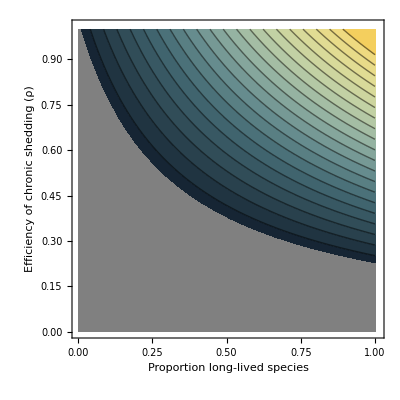

```mathematica
Fig1=ContourPlot[MSR0/.PlotPars,{Subscript[p, w],0,1},{ρ,0,1},FrameLabel->{"Proportion long-lived species","Efficiency of chronic shedding (ρ)"},BaseStyle->{FontSize->12,FontColor->Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},PlotRange->{{0,1.01},{0,1.01},{1,All}},PlotRangeClipping->True,ColorFunction->ColorData["StarryNightColors"],Contours->20,ImageSize->400,ColorFunctionScaling->True,ContourLabels->False,ClippingStyle->CMYKColor[0.5,0.5,0.5,0]]
```

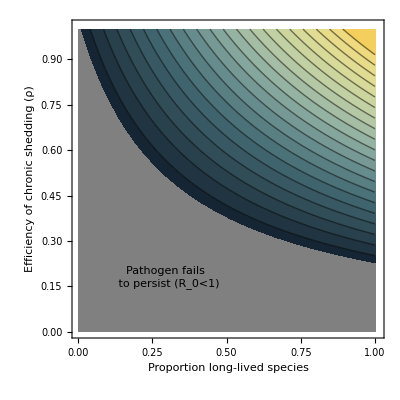

```mathematica
R0Fig=GraphicsRow[{Show[{Fig1},Epilog->{Inset["Pathogen fails \n to persist (R_0<1)",{0.3,0.18}]}],MyLegend}]
```

```mathematica
Export[outpath<>"/Fig3.pdf",R0Fig]
```

/home/nuismer/Work/Manuscripts/MTPOL/Figures/Fig3.pdf

## Force of Spillover/Infection Figures

This section requires that the previous sections be run first.

#### Plotting Tools

Define R_0:

```mathematica
MSR0Check=FullSimplify[Sum[(Subscript[L, i] (β δ+α ξ Subscript[n, t]) (1+Subscript[L, i] γ ρ) Subscript[p, i])/(δ(1+Subscript[L, i] γ ))/.{Subscript[L, i]->1/Subscript[μ, i]},{i,SpeciesIndices}]]
```

((β δ+α ξ n_t) ((p_w (γ ρ+μ_w))/(μ_w (γ+μ_w))+(p_x (γ ρ+μ_x))/(μ_x (γ+μ_x))+(p_y (γ ρ+μ_y))/(μ_y (γ+μ_y))+(p_z (γ ρ+μ_z))/(μ_z (γ+μ_z))))/δ

Define the ODE’s:

```mathematica
AAEdsdt=Table[Subscript[s, i]'[t]==Subscript[b, i]-Sum[β Subscript[s, i][t]Subscript[ι, j][t]+ρ β Subscript[s, i][t](Subscript[r, j][t]+Subscript[q, j][t]),{j,SpeciesIndices}]- ξ Subscript[s, i][t]B[t]-Subscript[μ, i] Subscript[s, i][t],{i,SpeciesIndices}]/.SubFD;
```

```mathematica
AAEdidt=Table[Subscript[ι, i]'[t]==Sum[β Subscript[s, i][t]Subscript[ι, j][t]+ρ β Subscript[s, i][t](Subscript[r, j][t]+Subscript[q, j][t]),{j,SpeciesIndices}]+ ξ Subscript[s, i][t]B[t]-Subscript[μ, i] Subscript[ι, i][t]-γ Subscript[ι, i][t],{i,SpeciesIndices}]/.SubFD;
```

```mathematica
AAEdrdt=Table[Subscript[r, i]'[t]==γ Subscript[ι, i][t]-ω Subscript[r, i][t]-Subscript[μ, i] Subscript[r, i][t],{i,SpeciesIndices}]/.SubFD;
```

```mathematica
AAEdqdt=Table[Subscript[q, i]'[t]==ω Subscript[r, i][t]-Subscript[μ, i] Subscript[q, i][t],{i,SpeciesIndices}]/.SubFD;
```

```mathematica
AAEdbdt={B'[t]==Sum[α Subscript[ι, i][t]+ρ α(Subscript[r, i][t]+Subscript[q, i][t]),{i,SpeciesIndices}]-δ B[t]}/.SubFD;
```

Define replacements to convert ODE’s to steady state expressions:

```mathematica
SSVar=Join[Table[Subscript[s, i]'[t]->0,{i,SpeciesIndices}],Table[Subscript[ι, i]'[t]->0,{i,SpeciesIndices}],Table[Subscript[r, i]'[t]->0,{i,SpeciesIndices}],Table[Subscript[q, i]'[t]->0,{i,SpeciesIndices}],{B'[t]->0}]
```

{s_w'[t]→0,s_x'[t]→0,s_y'[t]→0,s_z'[t]→0,ι_w'[t]→0,ι_x'[t]→0,ι_y'[t]→0,ι_z'[t]→0,r_w'[t]→0,r_x'[t]→0,r_y'[t]→0,r_z'[t]→0,q_w'[t]→0,q_x'[t]→0,q_y'[t]→0,q_z'[t]→0,B'[t]→0}

```mathematica
AllVar=Join[Table[Subscript[s, i][t],{i,SpeciesIndices}],Table[Subscript[ι, i][t],{i,SpeciesIndices}],Table[Subscript[r, i][t],{i,SpeciesIndices}],Table[Subscript[q, i][t],{i,SpeciesIndices}],{B[t]}]
```

{s_w[t],s_x[t],s_y[t],s_z[t],ι_w[t],ι_x[t],ι_y[t],ι_z[t],r_w[t],r_x[t],r_y[t],r_z[t],q_w[t],q_x[t],q_y[t],q_z[t],B[t]}

Define the total population size:

```mathematica
PopSize=Total[Flatten[Join[Table[Subscript[s, i][t],{i,SpeciesIndices}],Table[Subscript[ι, i][t],{i,SpeciesIndices}],Table[Subscript[r, i][t],{i,SpeciesIndices}],Table[Subscript[q, i][t],{i,SpeciesIndices}]]]]
```

q_w[t]+q_x[t]+q_y[t]+q_z[t]+r_w[t]+r_x[t]+r_y[t]+r_z[t]+s_w[t]+s_x[t]+s_y[t]+s_z[t]+ι_w[t]+ι_x[t]+ι_y[t]+ι_z[t]

Join the equations into a single list and transform them to steady-state:

```mathematica
SSEq=Join[AAEdsdt,AAEdidt,AAEdrdt,AAEdqdt,AAEdbdt]/.SSVar;
```

Define the force of infection into the human population as described in the main text:

```mathematica
SpillForceFD=(Subscript[ι, w][t]+Subscript[ι, x][t]+Subscript[ι, y][t]+Subscript[ι, z][t])/PopSize+ρ(Subscript[r, w][t]+Subscript[r, x][t]+Subscript[r, y][t]+Subscript[r, z][t]+Subscript[q, w][t]+Subscript[q, x][t]+Subscript[q, y][t]+Subscript[q, z][t])/PopSize;
```

Define the pooled seroprevalence within the livestock herd:

```mathematica
SeroP=(Subscript[ι, w][t]+Subscript[ι, x][t]+Subscript[ι, y][t]+Subscript[ι, z][t]+Subscript[r, w][t]+Subscript[r, x][t]+Subscript[r, y][t]+Subscript[r, z][t])/PopSize;
```

#### Parameter combination #1

Here we start with a trace of camels and then increase camel number while reduce abundance of other livestock species. Thus, camels are assumed to be replacing other species uniformly.

```mathematica
SimPars={Nherd->402,Cam0->1,β->0.00015,ξ->.0004,α->.0002,δ->1/21,γ->1/(1*365),ω->1/(10*365),Subscript[μ, w]->1/(Cam*365),Subscript[μ, x]->1/(Cow*365),Subscript[μ, y]->1/(She*365),Subscript[μ, z]->1/(Goa*365)};
```

```mathematica
(ξ α)/δ/.SimPars
```

1.68×10^-6

Create a region plot that delineates the parameter combinations for which R_0>1:

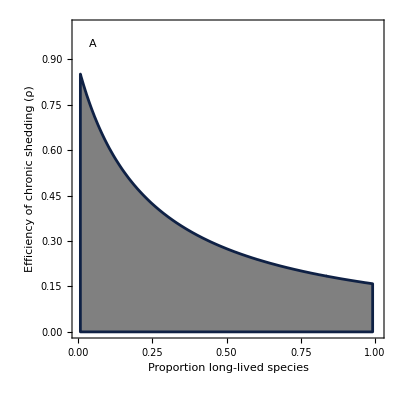

```mathematica
R0Reg1=RegionPlot[(MSR0Check/.SimPars/.{Subscript[p, x]->(1-Subscript[p, w])/3,Subscript[p, y]->(1-Subscript[p, w])/3,Subscript[p, z]->(1-Subscript[p, w])/3}/.Subscript[n, t]->Nherd/.SimPars)<1,{Subscript[p, w],0.008,.992},{ρ,0,1},BoundaryStyle->CMYKColor[0.83,0.63,0.23,0.65],PlotStyle->CMYKColor[0.5,0.5,0.5,0],FrameLabel->{"Proportion long-lived species","Efficiency of chronic shedding (ρ)"},BaseStyle->{FontSize->14,FontColor->Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},PlotRange->{{0,1.01},{0,1.01}},ImageSize->400,Epilog->Inset["A", {0.05,0.95}]]
```

Calculate steady-state values for force of infection into the human population and pooled livestock seroprevalence by looping through combinations of ρ and proportion of livestock that are camels:

```mathematica
Module[{i,j},StoreMe3={};For[i=0,i<11,i++,Camels=(Cam0/.SimPars)+40*i;For[j=0,j<11,j++,RhoRep={ρ->0.0+j*.1};BirthPars={Subscript[b, w]->Camels*Subscript[μ, w],Subscript[b, x]->(Nherd-Camels)/2*Subscript[μ, x],Subscript[b, y]->(Nherd-Camels)/4*Subscript[μ, y],Subscript[b, z]->(Nherd-Camels)/4*Subscript[μ, z]}/.SimPars;NumSol=NSolve[SSEq/.Subscript[n, t]->Nherd/.SimPars/.RhoRep/.BirthPars,AllVar,NonNegativeReals,Method->"Monodromy"];If[Length[NumSol]==0,NumSol={Subscript[s, w][t]->Subscript[b, w]/Subscript[μ, w]/.SimPars/.BirthPars,Subscript[s, x][t]->Subscript[b, x]/Subscript[μ, x]/.SimPars/.BirthPars,Subscript[s, y][t]->Subscript[b, y]/Subscript[μ, y]/.SimPars/.BirthPars,Subscript[s, z][t]->Subscript[b, z]/Subscript[μ, z]/.SimPars/.BirthPars,Subscript[ι, w][t]->0,Subscript[ι, x][t]->0,Subscript[ι, y][t]->0,Subscript[ι, z][t]->0,Subscript[r, w][t]->0,Subscript[r, x][t]->0,Subscript[r, y][t]->0,Subscript[r, z][t]->0,Subscript[q, w][t]->0,Subscript[q, x][t]->0,Subscript[q, y][t]->0,Subscript[q, z][t]->0,B[t]->0},NumSol=NumSol[[1]]];LS=((Subscript[b, w]/Subscript[μ, w])/(Subscript[b, w]/Subscript[μ, w]+Subscript[b, x]/Subscript[μ, x]+Subscript[b, y]/Subscript[μ, y]+Subscript[b, z]/Subscript[μ, z])1/Subscript[μ, w]+(Subscript[b, x]/Subscript[μ, x])/(Subscript[b, w]/Subscript[μ, w]+Subscript[b, x]/Subscript[μ, x]+Subscript[b, y]/Subscript[μ, y]+Subscript[b, z]/Subscript[μ, z])1/Subscript[μ, x]+(Subscript[b, y]/Subscript[μ, y])/(Subscript[b, w]/Subscript[μ, w]+Subscript[b, x]/Subscript[μ, x]+Subscript[b, y]/Subscript[μ, y]+Subscript[b, z]/Subscript[μ, z])1/Subscript[μ, y]+(Subscript[b, z]/Subscript[μ, z])/(Subscript[b, w]/Subscript[μ, w]+Subscript[b, x]/Subscript[μ, x]+Subscript[b, y]/Subscript[μ, y]+Subscript[b, z]/Subscript[μ, z])1/Subscript[μ, z])/365/.BirthPars/.SimPars;Wprev=(Subscript[ι, w][t]+Subscript[r, w][t])/(Subscript[b, w]/Subscript[μ, w])/.NumSol/.BirthPars/.SimPars;Xprev=(Subscript[ι, x][t]+Subscript[r, x][t])/(Subscript[b, x]/Subscript[μ, x])/.NumSol/.BirthPars/.SimPars;Yprev=(Subscript[ι, y][t]+Subscript[r, y][t])/(Subscript[b, y]/Subscript[μ, y])/.NumSol/.BirthPars/.SimPars;Zprev=(Subscript[ι, z][t]+Subscript[r, z][t])/(Subscript[b, z]/Subscript[μ, z])/.NumSol/.BirthPars/.SimPars;
Wforce=((Subscript[ι, w][t])/(Subscript[b, w]/Subscript[μ, w])+ρ(Subscript[r, w][t]+Subscript[q, w][t])/(Subscript[b, w]/Subscript[μ, w]))/.NumSol/.BirthPars/.SimPars/.RhoRep;Xforce=((Subscript[ι, x][t])/(Subscript[b, x]/Subscript[μ, x])+ρ(Subscript[r, x][t]+Subscript[q, x][t])/(Subscript[b, x]/Subscript[μ, x]))/.NumSol/.BirthPars/.SimPars/.RhoRep;Yforce=((Subscript[ι, y][t])/(Subscript[b, y]/Subscript[μ, y])+ρ(Subscript[r, y][t]+Subscript[q, y][t])/(Subscript[b, y]/Subscript[μ, y]))/.NumSol/.BirthPars/.SimPars/.RhoRep;Zforce=((Subscript[ι, z][t])/(Subscript[b, z]/Subscript[μ, z])+ρ(Subscript[r, z][t]+Subscript[q, z][t])/(Subscript[b, z]/Subscript[μ, z]))/.NumSol/.BirthPars/.SimPars/.RhoRep;

PW=(Subscript[b, w]/Subscript[μ, w])/(Subscript[b, w]/Subscript[μ, w]+Subscript[b, x]/Subscript[μ, x]+Subscript[b, y]/Subscript[μ, y]+Subscript[b, z]/Subscript[μ, z])/.BirthPars/.SimPars;
PX=(Subscript[b, x]/Subscript[μ, x])/(Subscript[b, w]/Subscript[μ, w]+Subscript[b, x]/Subscript[μ, x]+Subscript[b, y]/Subscript[μ, y]+Subscript[b, z]/Subscript[μ, z])/.BirthPars/.SimPars;
PY=(Subscript[b, y]/Subscript[μ, y])/(Subscript[b, w]/Subscript[μ, w]+Subscript[b, x]/Subscript[μ, x]+Subscript[b, y]/Subscript[μ, y]+Subscript[b, z]/Subscript[μ, z])/.BirthPars/.SimPars;
PZ=(Subscript[b, z]/Subscript[μ, z])/(Subscript[b, w]/Subscript[μ, w]+Subscript[b, x]/Subscript[μ, x]+Subscript[b, y]/Subscript[μ, y]+Subscript[b, z]/Subscript[μ, z])/.BirthPars/.SimPars;
HerdSize=(Subscript[b, w]/Subscript[μ, w]+Subscript[b, x]/Subscript[μ, x]+Subscript[b, y]/Subscript[μ, y]+Subscript[b, z]/Subscript[μ, z])/.BirthPars/.SimPars;ThisR0=MSR0Check/.SimPars/.RhoRep/.{Subscript[p, w]->PW,Subscript[p, x]->PX,Subscript[p, y]->PY,Subscript[p, z]->PZ}/.Subscript[n, t]->HerdSize;
CheckSize=PopSize/.NumSol;StoreMe3=Append[StoreMe3,Flatten[{N[LS],ρ/.RhoRep,SpillForceFD/.NumSol/.SimPars/.RhoRep,SeroP/.NumSol,ThisR0,Wprev,Xprev,Yprev,Zprev,Wforce,Xforce,Yforce,Zforce,PW,PX,PY,PZ,HerdSize,CheckSize}]]]]]
```

Make a plot of force of spillover using the values generated in the loop above:

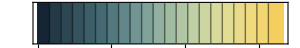

```mathematica
MyFOILegend=ContourPlot[x,{x,0,1},{y,0,1},Contours->20,ColorFunctionScaling->False,ColorFunction->ColorData["StarryNightColors"],BaseStyle->{FontSize->12,FontColor->Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},LabelStyle->Directive[FontSize->14,FontColor->Black],AspectRatio->.1,FrameTicks->{Automatic,None},FrameLabel->{None,None,"Force of infection",None},ImageSize->300]
```

```mathematica
SetRange={{5,15},{0,0.7}};
```

```mathematica
ToPlot1=StoreMe3[[All,{14,2,3}]];
```

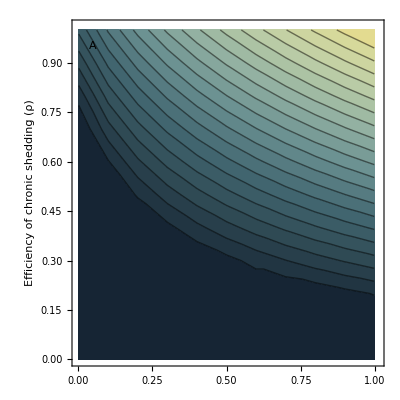

```mathematica
SpillRisk=ListContourPlot[ToPlot1,InterpolationOrder->5,FrameLabel->{"","Efficiency of chronic shedding (ρ)"},BaseStyle->{FontSize->14,FontColor->Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},PlotRange->{{0,1.01},{0,1.01},{0,All}},PlotRangeClipping->True,ColorFunction->ColorData["StarryNightColors"],Contours->20,ColorFunctionScaling->False,ImageSize->400,ContourLabels->False,Epilog->Inset["A", {0.05,0.95}]]
```

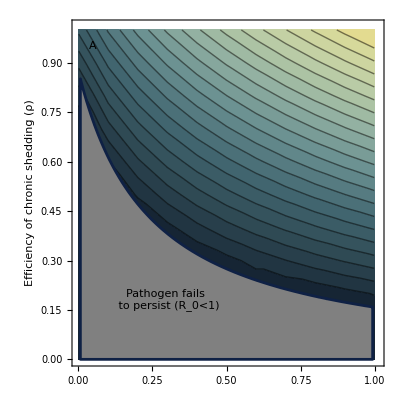

```mathematica
PanelA=GraphicsRow[{Show[{SpillRisk,R0Reg1},Epilog->{Inset["Pathogen fails \n to persist (R_0<1)",{0.3,0.18}],Inset["A",{0.05,0.95}]}]}]
```

Make a plot of pooled livestock seroprevalence using the values generated in the loop above:

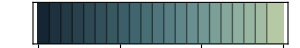

```mathematica
MySeroLegend=ContourPlot[x,{x,0,0.6},{y,0,1},Contours->20,ColorFunctionScaling->False,ColorFunction->ColorData["StarryNightColors"],BaseStyle->{FontSize->12,FontColor->Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},LabelStyle->Directive[FontSize->14,FontColor->Black],AspectRatio->.1,FrameTicks->{Automatic,None},FrameLabel->{None,None,"Seroprevalence",None},ImageSize->300]
```

```mathematica
ToPlotSero1=StoreMe3[[All,{14,2,4}]];
```

Set manual contour intervals:

```mathematica
MyContours=Table[0.0+.025 i,{i,1,24}]
```

{0.025,0.05,0.075,0.1,0.125,0.15,0.175,0.2,0.225,0.25,0.275,0.3,0.325,0.35,0.375,0.4,0.425,0.45,0.475,0.5,0.525,0.55,0.575,0.6}

Make the contour interval corresponding to pooled livestock seroprevalence in the data a white dashed line:

```mathematica
MyColors=Table[If[i!=5,{Thin,Black},{Thick,White,Dashing[.02]}],{i,1,24}]
```

{{Thickness[Tiny],GrayLevel[0]},{Thickness[Tiny],GrayLevel[0]},{Thickness[Tiny],GrayLevel[0]},{Thickness[Tiny],GrayLevel[0]},{Thickness[Large],GrayLevel[1],Dashing[0.02]},{Thickness[Tiny],GrayLevel[0]},{Thickness[Tiny],GrayLevel[0]},{Thickness[Tiny],GrayLevel[0]},{Thickness[Tiny],GrayLevel[0]},{Thickness[Tiny],GrayLevel[0]},{Thickness[Tiny],GrayLevel[0]},{Thickness[Tiny],GrayLevel[0]},{Thickness[Tiny],GrayLevel[0]},{Thickness[Tiny],GrayLevel[0]},{Thickness[Tiny],GrayLevel[0]},{Thickness[Tiny],GrayLevel[0]},{Thickness[Tiny],GrayLevel[0]},{Thickness[Tiny],GrayLevel[0]},{Thickness[Tiny],GrayLevel[0]},{Thickness[Tiny],GrayLevel[0]},{Thickness[Tiny],GrayLevel[0]},{Thickness[Tiny],GrayLevel[0]},{Thickness[Tiny],GrayLevel[0]},{Thickness[Tiny],GrayLevel[0]}}

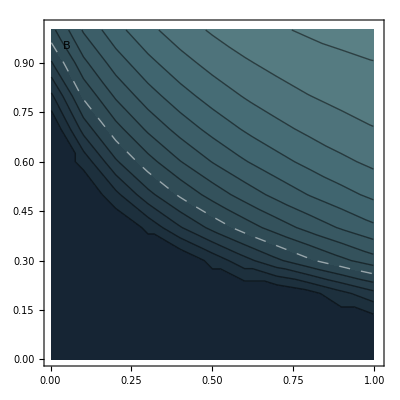

```mathematica
Sero=ListContourPlot[ToPlotSero1,InterpolationOrder->5,FrameLabel->{"",""},BaseStyle->{FontSize->14,FontColor->Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},PlotRange->{{0,1.01},{0,1.01},{0,All}},PlotRangeClipping->True,ColorFunction->ColorData["StarryNightColors"],ColorFunctionScaling->False,ImageSize->400,Contours->MyContours,ContourLabels->False,ContourStyle->MyColors,Epilog->Inset["B", {0.05,0.95}]]
```

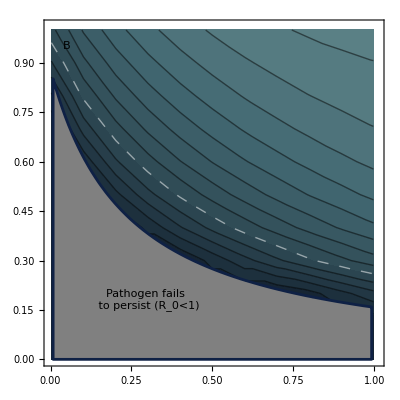

```mathematica
PanelB=GraphicsRow[{Show[{Sero,R0Reg1},Epilog->{Inset["Pathogen fails \n to persist (R_0<1)",{0.3,0.18}],Inset["B",{0.05,0.95}]}]}]
```

#### Parameter combination #2

Here we repeat the same steps as above but using a second set of parameters which we know will cause the lifespan effect to reverse.

```mathematica
SimPars={Nherd->402,Cam0->1,β->0.00045,ξ->.0005,α->.0004,δ->1/21,γ->1/(5*365),ω->1/(10*365),Subscript[μ, w]->1/(Cam*365),Subscript[μ, x]->1/(Cow*365),Subscript[μ, y]->1/(She*365),Subscript[μ, z]->1/(Goa*365)};
```

```mathematica
(ξ α)/δ/.SimPars
```

4.2×10^-6

Create a region plot delineating the area where R_0>1. For this specific set of parameters the entire panel is white because all parameter combinations yield R_0 values above 1.

```mathematica
R0Reg2=RegionPlot[(MSR0Check/.SimPars/.{Subscript[p, x]->(1-Subscript[p, w])/3,Subscript[p, y]->(1-Subscript[p, w])/3,Subscript[p, z]->(1-Subscript[p, w])/3}/.Subscript[n, t]->Nherd/.SimPars)<1,{Subscript[p, w],0.008,.992},{ρ,0,1},BoundaryStyle->CMYKColor[0.83,0.63,0.23,0.65],PlotStyle->CMYKColor[0.5,0.5,0.5,0],FrameLabel->{"Proportion long-lived species","Efficiency of chronic shedding (ρ)"},BaseStyle->{FontSize->12,FontColor->Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},PlotRange->{{0,1.01},{0,1.01}},ImageSize->400]
```

-Graphics-

Solve for steady state force of infection and seroprevalence by looping over parameter combinations:

```mathematica
Module[{i,j},StoreMe3={};For[i=0,i<11,i++,Camels=(Cam0/.SimPars)+40*i;For[j=0,j<11,j++,RhoRep={ρ->0.0+j*.1};BirthPars={Subscript[b, w]->Camels*Subscript[μ, w],Subscript[b, x]->(Nherd-Camels)/2*Subscript[μ, x],Subscript[b, y]->(Nherd-Camels)/4*Subscript[μ, y],Subscript[b, z]->(Nherd-Camels)/4*Subscript[μ, z]}/.SimPars;NumSol=NSolve[SSEq/.Subscript[n, t]->Nherd/.SimPars/.RhoRep/.BirthPars,AllVar,NonNegativeReals,Method->"Monodromy"];If[Length[NumSol]==0,NumSol={Subscript[s, w][t]->Subscript[b, w]/Subscript[μ, w]/.SimPars/.BirthPars,Subscript[s, x][t]->Subscript[b, x]/Subscript[μ, x]/.SimPars/.BirthPars,Subscript[s, y][t]->Subscript[b, y]/Subscript[μ, y]/.SimPars/.BirthPars,Subscript[s, z][t]->Subscript[b, z]/Subscript[μ, z]/.SimPars/.BirthPars,Subscript[ι, w][t]->0,Subscript[ι, x][t]->0,Subscript[ι, y][t]->0,Subscript[ι, z][t]->0,Subscript[r, w][t]->0,Subscript[r, x][t]->0,Subscript[r, y][t]->0,Subscript[r, z][t]->0,Subscript[q, w][t]->0,Subscript[q, x][t]->0,Subscript[q, y][t]->0,Subscript[q, z][t]->0,B[t]->0},NumSol=NumSol[[1]]];LS=((Subscript[b, w]/Subscript[μ, w])/(Subscript[b, w]/Subscript[μ, w]+Subscript[b, x]/Subscript[μ, x]+Subscript[b, y]/Subscript[μ, y]+Subscript[b, z]/Subscript[μ, z])1/Subscript[μ, w]+(Subscript[b, x]/Subscript[μ, x])/(Subscript[b, w]/Subscript[μ, w]+Subscript[b, x]/Subscript[μ, x]+Subscript[b, y]/Subscript[μ, y]+Subscript[b, z]/Subscript[μ, z])1/Subscript[μ, x]+(Subscript[b, y]/Subscript[μ, y])/(Subscript[b, w]/Subscript[μ, w]+Subscript[b, x]/Subscript[μ, x]+Subscript[b, y]/Subscript[μ, y]+Subscript[b, z]/Subscript[μ, z])1/Subscript[μ, y]+(Subscript[b, z]/Subscript[μ, z])/(Subscript[b, w]/Subscript[μ, w]+Subscript[b, x]/Subscript[μ, x]+Subscript[b, y]/Subscript[μ, y]+Subscript[b, z]/Subscript[μ, z])1/Subscript[μ, z])/365/.BirthPars/.SimPars;Wprev=(Subscript[ι, w][t]+Subscript[r, w][t])/(Subscript[b, w]/Subscript[μ, w])/.NumSol/.BirthPars/.SimPars;Xprev=(Subscript[ι, x][t]+Subscript[r, x][t])/(Subscript[b, x]/Subscript[μ, x])/.NumSol/.BirthPars/.SimPars;Yprev=(Subscript[ι, y][t]+Subscript[r, y][t])/(Subscript[b, y]/Subscript[μ, y])/.NumSol/.BirthPars/.SimPars;Zprev=(Subscript[ι, z][t]+Subscript[r, z][t])/(Subscript[b, z]/Subscript[μ, z])/.NumSol/.BirthPars/.SimPars;
Wforce=((Subscript[ι, w][t])/(Subscript[b, w]/Subscript[μ, w])+ρ(Subscript[r, w][t]+Subscript[q, w][t])/(Subscript[b, w]/Subscript[μ, w]))/.NumSol/.BirthPars/.SimPars/.RhoRep;Xforce=((Subscript[ι, x][t])/(Subscript[b, x]/Subscript[μ, x])+ρ(Subscript[r, x][t]+Subscript[q, x][t])/(Subscript[b, x]/Subscript[μ, x]))/.NumSol/.BirthPars/.SimPars/.RhoRep;Yforce=((Subscript[ι, y][t])/(Subscript[b, y]/Subscript[μ, y])+ρ(Subscript[r, y][t]+Subscript[q, y][t])/(Subscript[b, y]/Subscript[μ, y]))/.NumSol/.BirthPars/.SimPars/.RhoRep;Zforce=((Subscript[ι, z][t])/(Subscript[b, z]/Subscript[μ, z])+ρ(Subscript[r, z][t]+Subscript[q, z][t])/(Subscript[b, z]/Subscript[μ, z]))/.NumSol/.BirthPars/.SimPars/.RhoRep;

PW=(Subscript[b, w]/Subscript[μ, w])/(Subscript[b, w]/Subscript[μ, w]+Subscript[b, x]/Subscript[μ, x]+Subscript[b, y]/Subscript[μ, y]+Subscript[b, z]/Subscript[μ, z])/.BirthPars/.SimPars;
PX=(Subscript[b, x]/Subscript[μ, x])/(Subscript[b, w]/Subscript[μ, w]+Subscript[b, x]/Subscript[μ, x]+Subscript[b, y]/Subscript[μ, y]+Subscript[b, z]/Subscript[μ, z])/.BirthPars/.SimPars;
PY=(Subscript[b, y]/Subscript[μ, y])/(Subscript[b, w]/Subscript[μ, w]+Subscript[b, x]/Subscript[μ, x]+Subscript[b, y]/Subscript[μ, y]+Subscript[b, z]/Subscript[μ, z])/.BirthPars/.SimPars;
PZ=(Subscript[b, z]/Subscript[μ, z])/(Subscript[b, w]/Subscript[μ, w]+Subscript[b, x]/Subscript[μ, x]+Subscript[b, y]/Subscript[μ, y]+Subscript[b, z]/Subscript[μ, z])/.BirthPars/.SimPars;
HerdSize=(Subscript[b, w]/Subscript[μ, w]+Subscript[b, x]/Subscript[μ, x]+Subscript[b, y]/Subscript[μ, y]+Subscript[b, z]/Subscript[μ, z])/.BirthPars/.SimPars;ThisR0=MSR0Check/.SimPars/.RhoRep/.{Subscript[p, w]->PW,Subscript[p, x]->PX,Subscript[p, y]->PY,Subscript[p, z]->PZ}/.Subscript[n, t]->HerdSize;
CheckSize=PopSize/.NumSol;StoreMe3=Append[StoreMe3,Flatten[{N[LS],ρ/.RhoRep,SpillForceFD/.NumSol/.SimPars/.RhoRep,SeroP/.NumSol,ThisR0,Wprev,Xprev,Yprev,Zprev,Wforce,Xforce,Yforce,Zforce,PW,PX,PY,PZ,HerdSize,CheckSize}]]]]]
```

Generate a plot for force of spillover into the human population:

```mathematica
SetRange={{5,15},{0,0.7}};
```

```mathematica
ToPlotFOI2=StoreMe3[[All,{14,2,3}]];
```

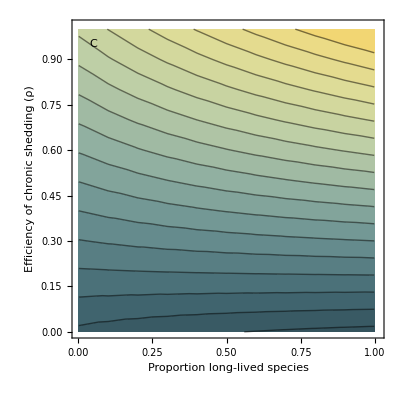

```mathematica
SpillRisk=ListContourPlot[ToPlotFOI2,InterpolationOrder->5,FrameLabel->{"Proportion long-lived species","Efficiency of chronic shedding (ρ)"},BaseStyle->{FontSize->14,FontColor->Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},PlotRange->{{0,1.01},{0,1.01},{0,All}},PlotRangeClipping->True,ColorFunction->ColorData["StarryNightColors"],Contours->20,ColorFunctionScaling->False,ImageSize->400,ContourLabels->False,Epilog->Inset["C", {0.05,0.95}]]
```

```mathematica
PanelC=GraphicsRow[{SpillRisk}]
```

-Graphics-

Generate a plot for seroprevalence in livestock:

```mathematica
ToPlotSero2=StoreMe3[[All,{14,2,4}]];
```

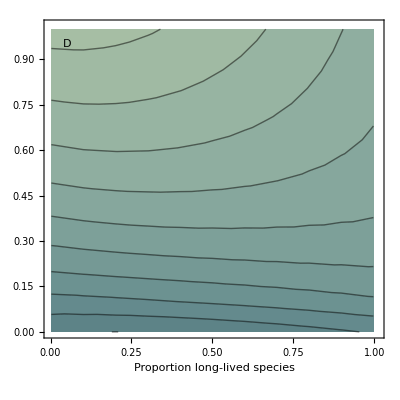

```mathematica
Sero=ListContourPlot[ToPlotSero2,InterpolationOrder->5,FrameLabel->{"Proportion long-lived species",""},BaseStyle->{FontSize->14,FontColor->Black},FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},PlotRange->{{0,1.01},{0,1.01},{0,All}},PlotRangeClipping->True,ColorFunction->ColorData["StarryNightColors"],ColorFunctionScaling->False,ImageSize->400,Epilog->Inset["D", {0.05,0.95}],Contours->MyContours,ContourLabels->False,ContourStyle->MyColors]
```

```mathematica
PanelD=GraphicsRow[{Sero}]
```

-Graphics-

#### Compile final figure

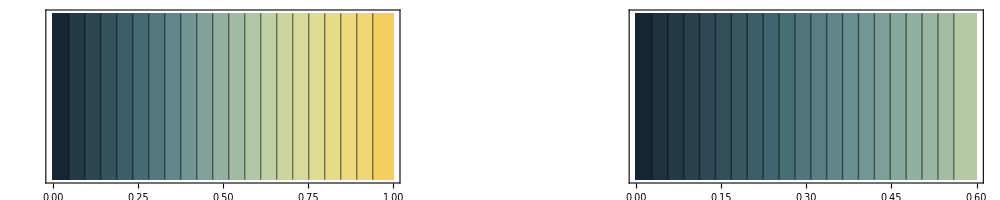

```mathematica
FOIFig=GraphicsGrid[{{MyFOILegend,MySeroLegend},{PanelA,PanelB},{PanelC,PanelD}},ImageSize->1000,Spacings->0,Alignment->{Center,Center}]
```

```mathematica
Export[outpath<>"/Fig4.pdf",FOIFig]
```

/home/nuismer/Work/Manuscripts/MTPOL/Figures/Fig4.pdf

# Import and Analyze Maximum Likelihood Solutions

## Set lifespans

Set lifespans to their estimated values

```mathematica
Cam=16;
Cow=6;
She=3;
Goa=2;
```

## Import maximum likelihood solutions

Import the ML solutions from their files:

```mathematica
MLDG2O15=Import[inpath<>"/Data/MLE Results/MLE_Village_Level_gamma2_omega15.csv"];
```

```mathematica
MLDG2O5=Import[inpath<>"/Data/MLE Results/MLE_Village_Level_gamma2_omega5.csv"];
```

```mathematica
MLDGHO15=Import[inpath<>"/Data/MLE Results/MLE_Village_Level_gammahalf_omega15.csv"];
```

```mathematica
MLDGHO5=Import[inpath<>"/Data/MLE Results/MLE_Village_Level_gammahalf_omega5.csv"];
```

Inspect the ML estimates for the 10 different random starting values:

```mathematica
MatrixForm[MLDG2O15]
```

(Column1 | A_start | beta_start | rho_start | A_hat | beta_hat | rho_hat | nloglik | code
1 | 0.0000144906 | 0.00205383 | 0.000305864 | 4.11156×10^-9 | 0.00219446 | 0.0577491 | 193.544 | 0
2 | 0.000148528 | 0.00147112 | 0.000373608 | 3.94781×10^-11 | 0.00192774 | 0.139697 | 205.319 | 10
3 | 8.41036×10^-7 | 0.00160036 | 0.000327562 | 7.40482×10^-8 | 0.00236611 | 0.00245825 | 227.172 | 10
4 | 0.00010116 | 0.00151215 | 0.00043651 | 2.25597×10^-13 | 0.00182583 | 0.177992 | 212.172 | 0
5 | 3.28636×10^-6 | 0.00146294 | 0.00055717 | 1.31343×10^-8 | 0.00229813 | 0.0291765 | 192.547 | 0
6 | 0.0000163693 | 0.00170335 | 0.000326472 | 1.78693×10^-11 | 0.00197935 | 0.121812 | 202.358 | 10
7 | 0.0000108734 | 0.00162583 | 0.000317137 | 1.31469×10^-8 | 0.0022984 | 0.0291078 | 192.547 | 0
8 | 0.0000536809 | 0.00140218 | 0.000570444 | 3.42545×10^-15 | 0.0014463 | 0.369116 | 243.846 | 0
9 | 0.0000833446 | 0.00150137 | 0.000379254 | 1.31385×10^-8 | 0.00229802 | 0.0292025 | 192.547 | 0
10 | 0.0000899698 | 0.00158367 | 0.000371279 | 2.81038×10^-8 | 0.00233736 | 0.0168488 | 195.075 | 0)

```mathematica
MatrixForm[MLDG2O5]
```

(Column1 | A_start | beta_start | rho_start | A_hat | beta_hat | rho_hat | nloglik | code
1 | 0.0000404329 | 0.00172406 | 0.000300051 | 1.51278×10^-8 | 0.001928 | 0.14009 | 162.999 | 10
2 | 0.0000760829 | 0.00137239 | 0.000538342 | 1.08781×10^-8 | 0.00183156 | 0.175716 | 163.851 | 0
3 | 0.000111808 | 0.00133994 | 0.000490287 | 2.0143×10^-8 | 0.00200021 | 0.11483 | 162.832 | 0
4 | 0.0000760321 | 0.00149468 | 0.000374577 | 2.01493×10^-8 | 0.00200043 | 0.114757 | 162.832 | 0
5 | 0.000016365 | 0.00216747 | 0.000315304 | 2.01665×10^-8 | 0.00200085 | 0.114613 | 162.832 | 0
6 | 0.0000730212 | 0.00117974 | 0.000552934 | 6.91367×10^-9 | 0.00189819 | 0.15371 | 163.693 | 0
7 | 0.000128672 | 0.00155961 | 0.000325939 | 8.09946×10^-9 | 0.00179385 | 0.191516 | 164.168 | 0
8 | 7.75197×10^-6 | 0.0015811 | 0.000303654 | 2.01293×10^-8 | 0.00200012 | 0.114864 | 162.832 | 0
9 | 0.0000650107 | 0.00141335 | 0.000565616 | 2.01606×10^-8 | 0.00200076 | 0.114644 | 162.832 | 0
10 | 0.0000633858 | 0.00176735 | 0.000313712 | 2.01276×10^-8 | 0.00200035 | 0.11479 | 162.832 | 0)

```mathematica
MatrixForm[MLDGHO15]
```

(Column1 | A_start | beta_start | rho_start | A_hat | beta_hat | rho_hat | nloglik | code
1 | 0.000052935 | 0.00192779 | 0.000419413 | 2.13763×10^-8 | 0.00544815 | 0.032431 | 164.135 | 0
2 | 0.0000638123 | 0.00215842 | 0.000322579 | 1.79983×10^-14 | 0.002382 | 0.263945 | 225.505 | 0
3 | 0.0000160576 | 0.00143469 | 0.000553783 | 9.26131×10^-8 | 0.00586221 | 0.0179425 | 163.526 | 0
4 | 0.000130161 | 0.00173788 | 0.000443854 | 2.85004×10^-15 | 0.00173844 | 0.417862 | 244.414 | 0
5 | 0.0000517593 | 0.00148236 | 0.000582551 | 2.19065×10^-15 | 0.00160343 | 0.465723 | 248.455 | 0
6 | 4.87651×10^-6 | 0.00187509 | 0.000394455 | 1.93482×10^-8 | 0.00280824 | 0.199856 | 225.038 | 10
7 | 0.0000443456 | 0.00208539 | 0.000419978 | 3.0396×10^-15 | 0.00185066 | 0.383336 | 241.04 | 0
8 | 8.13422×10^-6 | 0.00163359 | 0.000450556 | 5.4572×10^-16 | 0.00154089 | 0.490465 | 250.321 | 0
9 | 0.000164049 | 0.00195225 | 0.000331968 | 1.20489×10^-15 | 0.00188582 | 0.373518 | 239.997 | 0
10 | 0.000109883 | 0.0024447 | 0.0003215 | 7.32085×10^-15 | 0.00244751 | 0.253647 | 223.387 | 0)

```mathematica
MatrixForm[MLDGHO5]
```

(Column1 | A_start | beta_start | rho_start | A_hat | beta_hat | rho_hat | nloglik | code
1 | 0.0000708006 | 0.00224619 | 0.000318605 | 1.01364×10^-7 | 0.00476023 | 0.0574271 | 143.17 | 0
2 | 0.0000110685 | 0.00146225 | 0.000539835 | 1.24141×10^-9 | 0.00359231 | 0.128821 | 149.772 | 0
3 | 0.0000354637 | 0.00238113 | 0.000322828 | 1.0114×10^-7 | 0.00475938 | 0.0574642 | 143.17 | 0
4 | 0.000155199 | 0.00244513 | 0.000306409 | 1.01079×10^-7 | 0.0047596 | 0.0574594 | 143.17 | 0
5 | 0.0000307584 | 0.00207151 | 0.000326791 | 1.01142×10^-7 | 0.00475976 | 0.0574515 | 143.17 | 0
6 | 0.0000322505 | 0.00196553 | 0.000462471 | 1.01257×10^-7 | 0.00475846 | 0.0574888 | 143.17 | 0
7 | 0.000171976 | 0.00205503 | 0.000349559 | 1.02077×10^-7 | 0.00477427 | 0.0568071 | 143.173 | 0
8 | 0.0000737483 | 0.00223557 | 0.000351932 | 1.02118×10^-7 | 0.00477547 | 0.0567556 | 143.173 | 0
9 | 0.000151391 | 0.00155165 | 0.000455668 | 3.22994×10^-16 | 0.00269645 | 0.219544 | 151.894 | 0
10 | 1.5176×10^-6 | 0.00189812 | 0.000447306 | 1.01007×10^-7 | 0.00476001 | 0.0574489 | 143.17 | 0)

Pick the estimate with the best (smallest) likelihood from each set of fixed γ and ω values:

```mathematica
Module[{i},For[i=2,i<=Length[MLDG2O15],i++,If[MLDG2O15[[i,8]]==Min[MLDG2O15[[2;;All,8]]],MLDG2O15HAT=MLDG2O15[[i]]]]]
```

```mathematica
MLDG2O15HAT
```

{5,3.28636×10^-6,0.00146294,0.00055717,1.31343×10^-8,0.00229813,0.0291765,192.547,0}

```mathematica
Module[{i},For[i=2,i<=Length[MLDG2O5],i++,If[MLDG2O5[[i,8]]==Min[MLDG2O5[[2;;All,8]]],MLDG2O5HAT=MLDG2O5[[i]]]]]
```

```mathematica
MLDG2O5HAT
```

{4,0.0000760321,0.00149468,0.000374577,2.01493×10^-8,0.00200043,0.114757,162.832,0}

```mathematica
Module[{i},For[i=2,i<=Length[MLDGHO15],i++,If[MLDGHO15[[i,8]]==Min[MLDGHO15[[2;;All,8]]],MLDGHO15HAT=MLDGHO15[[i]]]]]
```

```mathematica
MLDGHO15HAT
```

{3,0.0000160576,0.00143469,0.000553783,9.26131×10^-8,0.00586221,0.0179425,163.526,0}

```mathematica
Module[{i},For[i=2,i<=Length[MLDGHO5],i++,If[MLDGHO5[[i,8]]==Min[MLDGHO5[[2;;All,8]]],MLDGHO5HAT=MLDGHO5[[i]]]]]
```

```mathematica
MLDGHO5HAT
```

{4,0.000155199,0.00244513,0.000306409,1.01079×10^-7,0.0047596,0.0574594,143.17,0}

## Import the village level data

```mathematica
VD=Import[inpath<>"/Data/Clean/village_level_data_w_FOI.csv"];
```

```mathematica
MatrixForm[VD]
```

(county | village | size_livestock | size_bovine | size_camel | size_goat | size_sheep | n_tested_livestock | n_tested_bovine | n_tested_camel | n_tested_goat | n_tested_sheep | n_positive_bovine | n_positive_camel | n_positive_goat | n_positive_sheep | n_negative_bovine | n_negative_camel | n_negative_goat | n_negative_sheep | n_tested_human | n_positive_human | n_negative_human | prop_bovine | prop_camel | prop_goat | prop_sheep | expected_herd_lifespan | expected_herd_lifespan_s | seroprevalence | lambda
Kajiado | Empukani | 1217 | 333 | 0 | 467 | 417 | 320 | 90 | 0 | 130 | 100 | 5 | 0 | 4 | 1 | 85 | 0 | 126 | 97 | 98 | 4 | 94 | 0.273624 | 0. | 0.38373 | 0.342646 | 3.43714 | -0.839969 | 0.0408163 | 0.00226089
Kajiado | Endonyo | 550 | 121 | 0 | 250 | 179 | 233 | 57 | 0 | 96 | 80 | 1 | 0 | 1 | 0 | 56 | 0 | 95 | 80 | 73 | 1 | 72 | 0.22 | 0. | 0.454545 | 0.325455 | 3.20545 | -1.21592 | 0.0136986 | 0.00109665
Kajiado | Ilumbwa | 814 | 280 | 0 | 271 | 263 | 210 | 55 | 0 | 79 | 76 | 0 | 0 | 1 | 0 | 55 | 0 | 78 | 76 | 52 | 3 | 49 | 0.34398 | 0. | 0.332924 | 0.323096 | 3.69902 | -0.415024 | 0.0576923 | 0.00200433
Kajiado | Kikeleya | 699 | 330 | 0 | 192 | 177 | 277 | 94 | 0 | 95 | 88 | 11 | 0 | 2 | 0 | 83 | 0 | 93 | 86 | 101 | 6 | 95 | 0.472103 | 0. | 0.274678 | 0.253219 | 4.14163 | 0.303202 | 0.0594059 | 0.00322205
Kajiado | Kisrket | 2132 | 754 | 0 | 794 | 584 | 415 | 148 | 0 | 144 | 123 | 10 | 0 | 1 | 0 | 138 | 0 | 143 | 112 | 145 | 12 | 133 | 0.353659 | 0. | 0.37242 | 0.273921 | 3.68856 | -0.432 | 0.0827586 | 0.00446998
Kajiado | Mailwa | 458 | 102 | 0 | 155 | 201 | 191 | 35 | 0 | 79 | 77 | 5 | 0 | 2 | 1 | 30 | 0 | 77 | 75 | 67 | 2 | 65 | 0.222707 | 0. | 0.338428 | 0.438865 | 3.32969 | -1.01432 | 0.0298507 | 0.00146145
Kajiado | Olchurai | 1055 | 422 | 0 | 349 | 284 | 203 | 67 | 0 | 71 | 65 | 4 | 0 | 2 | 0 | 63 | 0 | 69 | 65 | 70 | 2 | 68 | 0.4 | 0. | 0.330806 | 0.269194 | 3.86919 | -0.138879 | 0.0285714 | 0.00172166
Kajiado | Sere | 996 | 269 | 0 | 412 | 315 | 306 | 81 | 0 | 120 | 105 | 3 | 0 | 0 | 2 | 78 | 0 | 120 | 103 | 115 | 5 | 110 | 0.27008 | 0. | 0.413655 | 0.316265 | 3.39659 | -0.905776 | 0.0434783 | 0.00249274
Marsabit | Laisamis | 708 | 45 | 124 | 290 | 249 | 161 | 7 | 71 | 48 | 35 | 1 | 3 | 5 | 1 | 6 | 68 | 42 | 34 | 44 | 11 | 33 | 0.0635593 | 0.175141 | 0.409605 | 0.351695 | 5.05791 | 1.79004 | 0.25 | 0.0105524
Marsabit | Lontolio | 1254 | 129 | 152 | 615 | 358 | 374 | 39 | 112 | 144 | 79 | 6 | 11 | 15 | 1 | 32 | 101 | 129 | 78 | 85 | 11 | 74 | 0.102871 | 0.121212 | 0.490431 | 0.285486 | 4.39394 | 0.712621 | 0.129412 | 0.00576678
Marsabit | Nairibi | 588 | 56 | 23 | 346 | 163 | 224 | 43 | 18 | 103 | 60 | 2 | 1 | 2 | 0 | 41 | 17 | 101 | 60 | 78 | 10 | 68 | 0.0952381 | 0.0391156 | 0.588435 | 0.277211 | 3.20578 | -1.21539 | 0.128205 | 0.0065861
Marsabit | Ndikir | 2665 | 406 | 299 | 1260 | 700 | 497 | 63 | 161 | 166 | 107 | 5 | 9 | 17 | 8 | 58 | 150 | 149 | 98 | 123 | 17 | 106 | 0.152345 | 0.112195 | 0.472795 | 0.262664 | 4.44278 | 0.791869 | 0.138211 | 0.00773889
Marsabit | Sakardala | 2650 | 268 | 450 | 1121 | 811 | 675 | 91 | 335 | 169 | 80 | 15 | 37 | 19 | 4 | 76 | 298 | 150 | 76 | 130 | 24 | 106 | 0.101132 | 0.169811 | 0.423019 | 0.306038 | 5.08792 | 1.83875 | 0.184615 | 0.0114247
Marsabit | Silapani | 2792 | 249 | 303 | 1575 | 665 | 492 | 94 | 188 | 155 | 55 | 7 | 13 | 12 | 1 | 86 | 175 | 143 | 54 | 103 | 14 | 89 | 0.0891834 | 0.108524 | 0.564112 | 0.238181 | 4.11426 | 0.258779 | 0.135922 | 0.0066115
Marsabit | Trigamo | 5452 | 673 | 566 | 2552 | 1661 | 1049 | 172 | 397 | 302 | 178 | 20 | 50 | 29 | 9 | 152 | 347 | 273 | 169 | 196 | 28 | 168 | 0.123441 | 0.103815 | 0.468085 | 0.304659 | 4.25183 | 0.482028 | 0.142857 | 0.00773983)

Create a replacement rule using the expected lifespans set at the beginning of the notebook:

```mathematica
RepL={LCam->Cam,LCow->Cow,LSheep->She,LGoat->Goa};
```

Calculate the expected mixed-herd lifespan as a weighted average:

```mathematica
Lifespans=N[Table[VD[[i,5]]/VD[[i,3]] LCam+VD[[i,4]]/VD[[i,3]] LCow+VD[[i,7]]/VD[[i,3]] LSheep+VD[[i,6]]/VD[[i,3]] LGoat,{i,2,Length[VD]}]/.RepL]
```

{3.43714,3.20545,3.69902,4.14163,3.68856,3.32969,3.86919,3.39659,5.05791,4.39394,3.20578,4.44278,5.08792,4.11426,4.25183}

```mathematica
Elifetab=Prepend[Table[{VD[[i+1,1]],VD[[i+1,2]],Lifespans[[i]]},{i,1,Length[VD]-1}],{"County","Village","ELife"}]
```

{{County,Village,ELife},{Kajiado,Empukani,3.43714},{Kajiado,Endonyo,3.20545},{Kajiado,Ilumbwa,3.69902},{Kajiado,Kikeleya,4.14163},{Kajiado,Kisrket,3.68856},{Kajiado,Mailwa,3.32969},{Kajiado,Olchurai,3.86919},{Kajiado,Sere,3.39659},{Marsabit,Laisamis,5.05791},{Marsabit,Lontolio,4.39394},{Marsabit,Nairibi,3.20578},{Marsabit,Ndikir,4.44278},{Marsabit,Sakardala,5.08792},{Marsabit,Silapani,4.11426},{Marsabit,Trigamo,4.25183}}

Calculate birth and death rates from village level data and lifespans:

```mathematica
VDbandmu=N[Table[{VD[[i,1]],VD[[i,2]],VD[[i,5]]*1/(LCam*365),VD[[i,4]]*1/(LCow*365),VD[[i,7]]*1/(LSheep*365),VD[[i,6]]*1/(LGoat*365),1/(LCam*365),1/(LCow*365),1/(LSheep*365),1/(LGoat*365)},{i,2,Length[VD]}]/.RepL];
```

```mathematica
MatrixForm[VDbandmu]
```

(Kajiado | Empukani | 0. | 0.152055 | 0.380822 | 0.639726 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Kajiado | Endonyo | 0. | 0.0552511 | 0.16347 | 0.342466 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Kajiado | Ilumbwa | 0. | 0.127854 | 0.240183 | 0.371233 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Kajiado | Kikeleya | 0. | 0.150685 | 0.161644 | 0.263014 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Kajiado | Kisrket | 0. | 0.344292 | 0.533333 | 1.08767 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Kajiado | Mailwa | 0. | 0.0465753 | 0.183562 | 0.212329 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Kajiado | Olchurai | 0. | 0.192694 | 0.259361 | 0.478082 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Kajiado | Sere | 0. | 0.122831 | 0.287671 | 0.564384 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Marsabit | Laisamis | 0.0212329 | 0.0205479 | 0.227397 | 0.39726 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Marsabit | Lontolio | 0.0260274 | 0.0589041 | 0.326941 | 0.842466 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Marsabit | Nairibi | 0.00393836 | 0.0255708 | 0.148858 | 0.473973 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Marsabit | Ndikir | 0.0511986 | 0.185388 | 0.639269 | 1.72603 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Marsabit | Sakardala | 0.0770548 | 0.122374 | 0.740639 | 1.53562 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Marsabit | Silapani | 0.0518836 | 0.113699 | 0.607306 | 2.15753 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Marsabit | Trigamo | 0.0969178 | 0.307306 | 1.51689 | 3.49589 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986)

Add column headers:

```mathematica
ToSim=Prepend[VDbandmu,{"County","Village","bcam","bcow","bsheep","bgoat","dcam","dcow","dsheep","dgoat"}];
```

Inspect the final data set that we will use to define simulation parameters for each village:

```mathematica
MatrixForm[ToSim]
```

(County | Village | bcam | bcow | bsheep | bgoat | dcam | dcow | dsheep | dgoat
Kajiado | Empukani | 0. | 0.152055 | 0.380822 | 0.639726 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Kajiado | Endonyo | 0. | 0.0552511 | 0.16347 | 0.342466 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Kajiado | Ilumbwa | 0. | 0.127854 | 0.240183 | 0.371233 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Kajiado | Kikeleya | 0. | 0.150685 | 0.161644 | 0.263014 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Kajiado | Kisrket | 0. | 0.344292 | 0.533333 | 1.08767 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Kajiado | Mailwa | 0. | 0.0465753 | 0.183562 | 0.212329 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Kajiado | Olchurai | 0. | 0.192694 | 0.259361 | 0.478082 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Kajiado | Sere | 0. | 0.122831 | 0.287671 | 0.564384 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Marsabit | Laisamis | 0.0212329 | 0.0205479 | 0.227397 | 0.39726 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Marsabit | Lontolio | 0.0260274 | 0.0589041 | 0.326941 | 0.842466 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Marsabit | Nairibi | 0.00393836 | 0.0255708 | 0.148858 | 0.473973 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Marsabit | Ndikir | 0.0511986 | 0.185388 | 0.639269 | 1.72603 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Marsabit | Sakardala | 0.0770548 | 0.122374 | 0.740639 | 1.53562 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Marsabit | Silapani | 0.0518836 | 0.113699 | 0.607306 | 2.15753 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986
Marsabit | Trigamo | 0.0969178 | 0.307306 | 1.51689 | 3.49589 | 0.000171233 | 0.000456621 | 0.000913242 | 0.00136986)

## Simulate livestock seroprevalence and the force of infection into the human population

Here we use the values of livestock birth and death rates estimated from the village level data above, along with the maximum likelihood estimates for model parameters β, 𝒜, and ρ, and fixed values of the fixed parameters γ and ω  to simulate seroprevalence in livestock and the force of infection into the human population for each village. We then compare the simulated values to those estimated from the age-structured human seroprevalence data.

### First, set the simulation framework

Set the species sets for the the two counties. Kajiado lacks index w because it lacks camels.

```mathematica
SpeciesIndicesMars={w,x,y,z};
```

```mathematica
SpeciesIndicesKaj={x,y,z};
```

Create a replacement to move from livestock population sizes to birth and death rates

```mathematica
SubNMars={Subscript[n, t]->Sum[Subscript[b, i]/Subscript[μ, i],{i,SpeciesIndicesMars}]}
```

{n_t→b_w/μ_w+b_x/μ_x+b_y/μ_y+b_z/μ_z}

```mathematica
SubNKaj={Subscript[n, t]->Sum[Subscript[b, i]/Subscript[μ, i],{i,SpeciesIndicesKaj}]}
```

{n_t→b_x/μ_x+b_y/μ_y+b_z/μ_z}

Define the steady-state system of equations for each county. The system of equations differs across counties because Kajiado lacks camels.

```mathematica
QSSEQMars={0==Subscript[b, w]-Subscript[μ, w] Subscript[s, w][t]-(β ρ (Subscript[q, w][t]+Subscript[r, w][t]) Subscript[s, w][t])/Subscript[n, t]-(β ρ (Subscript[q, x][t]+Subscript[r, x][t]) Subscript[s, w][t])/Subscript[n, t]-(β ρ (Subscript[q, y][t]+Subscript[r, y][t]) Subscript[s, w][t])/Subscript[n, t]-(β ρ (Subscript[q, z][t]+Subscript[r, z][t]) Subscript[s, w][t])/Subscript[n, t]-(β Subscript[s, w][t] Subscript[ι, w][t])/Subscript[n, t]-(β Subscript[s, w][t] Subscript[ι, x][t])/Subscript[n, t]-(β Subscript[s, w][t] Subscript[ι, y][t])/Subscript[n, t]-(β Subscript[s, w][t] Subscript[ι, z][t])/Subscript[n, t]-𝒜 Subscript[s, w][t] (ρ (Subscript[q, w][t]+Subscript[q, x][t]+Subscript[q, y][t]+Subscript[q, z][t]+Subscript[r, w][t]+Subscript[r, x][t]+Subscript[r, y][t]+Subscript[r, z][t])+Subscript[ι, w][t]+Subscript[ι, x][t]+Subscript[ι, y][t]+Subscript[ι, z][t]),0==Subscript[b, x]-Subscript[μ, x] Subscript[s, x][t]-(β ρ (Subscript[q, w][t]+Subscript[r, w][t]) Subscript[s, x][t])/Subscript[n, t]-(β ρ (Subscript[q, x][t]+Subscript[r, x][t]) Subscript[s, x][t])/Subscript[n, t]-(β ρ (Subscript[q, y][t]+Subscript[r, y][t]) Subscript[s, x][t])/Subscript[n, t]-(β ρ (Subscript[q, z][t]+Subscript[r, z][t]) Subscript[s, x][t])/Subscript[n, t]-(β Subscript[s, x][t] Subscript[ι, w][t])/Subscript[n, t]-(β Subscript[s, x][t] Subscript[ι, x][t])/Subscript[n, t]-(β Subscript[s, x][t] Subscript[ι, y][t])/Subscript[n, t]-(β Subscript[s, x][t] Subscript[ι, z][t])/Subscript[n, t]-𝒜 Subscript[s, x][t] (ρ (Subscript[q, w][t]+Subscript[q, x][t]+Subscript[q, y][t]+Subscript[q, z][t]+Subscript[r, w][t]+Subscript[r, x][t]+Subscript[r, y][t]+Subscript[r, z][t])+Subscript[ι, w][t]+Subscript[ι, x][t]+Subscript[ι, y][t]+Subscript[ι, z][t]),0==Subscript[b, y]-Subscript[μ, y] Subscript[s, y][t]-(β ρ (Subscript[q, w][t]+Subscript[r, w][t]) Subscript[s, y][t])/Subscript[n, t]-(β ρ (Subscript[q, x][t]+Subscript[r, x][t]) Subscript[s, y][t])/Subscript[n, t]-(β ρ (Subscript[q, y][t]+Subscript[r, y][t]) Subscript[s, y][t])/Subscript[n, t]-(β ρ (Subscript[q, z][t]+Subscript[r, z][t]) Subscript[s, y][t])/Subscript[n, t]-(β Subscript[s, y][t] Subscript[ι, w][t])/Subscript[n, t]-(β Subscript[s, y][t] Subscript[ι, x][t])/Subscript[n, t]-(β Subscript[s, y][t] Subscript[ι, y][t])/Subscript[n, t]-(β Subscript[s, y][t] Subscript[ι, z][t])/Subscript[n, t]-𝒜 Subscript[s, y][t] (ρ (Subscript[q, w][t]+Subscript[q, x][t]+Subscript[q, y][t]+Subscript[q, z][t]+Subscript[r, w][t]+Subscript[r, x][t]+Subscript[r, y][t]+Subscript[r, z][t])+Subscript[ι, w][t]+Subscript[ι, x][t]+Subscript[ι, y][t]+Subscript[ι, z][t]),0==Subscript[b, z]-Subscript[μ, z] Subscript[s, z][t]-(β ρ (Subscript[q, w][t]+Subscript[r, w][t]) Subscript[s, z][t])/Subscript[n, t]-(β ρ (Subscript[q, x][t]+Subscript[r, x][t]) Subscript[s, z][t])/Subscript[n, t]-(β ρ (Subscript[q, y][t]+Subscript[r, y][t]) Subscript[s, z][t])/Subscript[n, t]-(β ρ (Subscript[q, z][t]+Subscript[r, z][t]) Subscript[s, z][t])/Subscript[n, t]-(β Subscript[s, z][t] Subscript[ι, w][t])/Subscript[n, t]-(β Subscript[s, z][t] Subscript[ι, x][t])/Subscript[n, t]-(β Subscript[s, z][t] Subscript[ι, y][t])/Subscript[n, t]-(β Subscript[s, z][t] Subscript[ι, z][t])/Subscript[n, t]-𝒜 Subscript[s, z][t] (ρ (Subscript[q, w][t]+Subscript[q, x][t]+Subscript[q, y][t]+Subscript[q, z][t]+Subscript[r, w][t]+Subscript[r, x][t]+Subscript[r, y][t]+Subscript[r, z][t])+Subscript[ι, w][t]+Subscript[ι, x][t]+Subscript[ι, y][t]+Subscript[ι, z][t]),0==(β ρ (Subscript[q, w][t]+Subscript[r, w][t]) Subscript[s, w][t])/Subscript[n, t]+(β ρ (Subscript[q, x][t]+Subscript[r, x][t]) Subscript[s, w][t])/Subscript[n, t]+(β ρ (Subscript[q, y][t]+Subscript[r, y][t]) Subscript[s, w][t])/Subscript[n, t]+(β ρ (Subscript[q, z][t]+Subscript[r, z][t]) Subscript[s, w][t])/Subscript[n, t]-γ Subscript[ι, w][t]-Subscript[μ, w] Subscript[ι, w][t]+(β Subscript[s, w][t] Subscript[ι, w][t])/Subscript[n, t]+(β Subscript[s, w][t] Subscript[ι, x][t])/Subscript[n, t]+(β Subscript[s, w][t] Subscript[ι, y][t])/Subscript[n, t]+(β Subscript[s, w][t] Subscript[ι, z][t])/Subscript[n, t]+𝒜 Subscript[s, w][t] (ρ (Subscript[q, w][t]+Subscript[q, x][t]+Subscript[q, y][t]+Subscript[q, z][t]+Subscript[r, w][t]+Subscript[r, x][t]+Subscript[r, y][t]+Subscript[r, z][t])+Subscript[ι, w][t]+Subscript[ι, x][t]+Subscript[ι, y][t]+Subscript[ι, z][t]),0==(β ρ (Subscript[q, w][t]+Subscript[r, w][t]) Subscript[s, x][t])/Subscript[n, t]+(β ρ (Subscript[q, x][t]+Subscript[r, x][t]) Subscript[s, x][t])/Subscript[n, t]+(β ρ (Subscript[q, y][t]+Subscript[r, y][t]) Subscript[s, x][t])/Subscript[n, t]+(β ρ (Subscript[q, z][t]+Subscript[r, z][t]) Subscript[s, x][t])/Subscript[n, t]+(β Subscript[s, x][t] Subscript[ι, w][t])/Subscript[n, t]-γ Subscript[ι, x][t]-Subscript[μ, x] Subscript[ι, x][t]+(β Subscript[s, x][t] Subscript[ι, x][t])/Subscript[n, t]+(β Subscript[s, x][t] Subscript[ι, y][t])/Subscript[n, t]+(β Subscript[s, x][t] Subscript[ι, z][t])/Subscript[n, t]+𝒜 Subscript[s, x][t] (ρ (Subscript[q, w][t]+Subscript[q, x][t]+Subscript[q, y][t]+Subscript[q, z][t]+Subscript[r, w][t]+Subscript[r, x][t]+Subscript[r, y][t]+Subscript[r, z][t])+Subscript[ι, w][t]+Subscript[ι, x][t]+Subscript[ι, y][t]+Subscript[ι, z][t]),0==(β ρ (Subscript[q, w][t]+Subscript[r, w][t]) Subscript[s, y][t])/Subscript[n, t]+(β ρ (Subscript[q, x][t]+Subscript[r, x][t]) Subscript[s, y][t])/Subscript[n, t]+(β ρ (Subscript[q, y][t]+Subscript[r, y][t]) Subscript[s, y][t])/Subscript[n, t]+(β ρ (Subscript[q, z][t]+Subscript[r, z][t]) Subscript[s, y][t])/Subscript[n, t]+(β Subscript[s, y][t] Subscript[ι, w][t])/Subscript[n, t]+(β Subscript[s, y][t] Subscript[ι, x][t])/Subscript[n, t]-γ Subscript[ι, y][t]-Subscript[μ, y] Subscript[ι, y][t]+(β Subscript[s, y][t] Subscript[ι, y][t])/Subscript[n, t]+(β Subscript[s, y][t] Subscript[ι, z][t])/Subscript[n, t]+𝒜 Subscript[s, y][t] (ρ (Subscript[q, w][t]+Subscript[q, x][t]+Subscript[q, y][t]+Subscript[q, z][t]+Subscript[r, w][t]+Subscript[r, x][t]+Subscript[r, y][t]+Subscript[r, z][t])+Subscript[ι, w][t]+Subscript[ι, x][t]+Subscript[ι, y][t]+Subscript[ι, z][t]),0==(β ρ (Subscript[q, w][t]+Subscript[r, w][t]) Subscript[s, z][t])/Subscript[n, t]+(β ρ (Subscript[q, x][t]+Subscript[r, x][t]) Subscript[s, z][t])/Subscript[n, t]+(β ρ (Subscript[q, y][t]+Subscript[r, y][t]) Subscript[s, z][t])/Subscript[n, t]+(β ρ (Subscript[q, z][t]+Subscript[r, z][t]) Subscript[s, z][t])/Subscript[n, t]+(β Subscript[s, z][t] Subscript[ι, w][t])/Subscript[n, t]+(β Subscript[s, z][t] Subscript[ι, x][t])/Subscript[n, t]+(β Subscript[s, z][t] Subscript[ι, y][t])/Subscript[n, t]-γ Subscript[ι, z][t]-Subscript[μ, z] Subscript[ι, z][t]+(β Subscript[s, z][t] Subscript[ι, z][t])/Subscript[n, t]+𝒜 Subscript[s, z][t] (ρ (Subscript[q, w][t]+Subscript[q, x][t]+Subscript[q, y][t]+Subscript[q, z][t]+Subscript[r, w][t]+Subscript[r, x][t]+Subscript[r, y][t]+Subscript[r, z][t])+Subscript[ι, w][t]+Subscript[ι, x][t]+Subscript[ι, y][t]+Subscript[ι, z][t]),0==-ω Subscript[r, w][t]-Subscript[μ, w] Subscript[r, w][t]+γ Subscript[ι, w][t],0==-ω Subscript[r, x][t]-Subscript[μ, x] Subscript[r, x][t]+γ Subscript[ι, x][t],0==-ω Subscript[r, y][t]-Subscript[μ, y] Subscript[r, y][t]+γ Subscript[ι, y][t],0==-ω Subscript[r, z][t]-Subscript[μ, z] Subscript[r, z][t]+γ Subscript[ι, z][t],0==-Subscript[μ, w] Subscript[q, w][t]+ω Subscript[r, w][t],0==-Subscript[μ, x] Subscript[q, x][t]+ω Subscript[r, x][t],0==-Subscript[μ, y] Subscript[q, y][t]+ω Subscript[r, y][t],0==-Subscript[μ, z] Subscript[q, z][t]+ω Subscript[r, z][t]}/.SubNMars;
```

```mathematica
QSSEQKaj={0==Subscript[b, x]-Subscript[μ, x] Subscript[s, x][t]-(β ρ (Subscript[q, w][t]+Subscript[r, w][t]) Subscript[s, x][t])/Subscript[n, t]-(β ρ (Subscript[q, x][t]+Subscript[r, x][t]) Subscript[s, x][t])/Subscript[n, t]-(β ρ (Subscript[q, y][t]+Subscript[r, y][t]) Subscript[s, x][t])/Subscript[n, t]-(β ρ (Subscript[q, z][t]+Subscript[r, z][t]) Subscript[s, x][t])/Subscript[n, t]-(β Subscript[s, x][t] Subscript[ι, w][t])/Subscript[n, t]-(β Subscript[s, x][t] Subscript[ι, x][t])/Subscript[n, t]-(β Subscript[s, x][t] Subscript[ι, y][t])/Subscript[n, t]-(β Subscript[s, x][t] Subscript[ι, z][t])/Subscript[n, t]-𝒜 Subscript[s, x][t] (ρ (Subscript[q, w][t]+Subscript[q, x][t]+Subscript[q, y][t]+Subscript[q, z][t]+Subscript[r, w][t]+Subscript[r, x][t]+Subscript[r, y][t]+Subscript[r, z][t])+Subscript[ι, w][t]+Subscript[ι, x][t]+Subscript[ι, y][t]+Subscript[ι, z][t]),0==Subscript[b, y]-Subscript[μ, y] Subscript[s, y][t]-(β ρ (Subscript[q, w][t]+Subscript[r, w][t]) Subscript[s, y][t])/Subscript[n, t]-(β ρ (Subscript[q, x][t]+Subscript[r, x][t]) Subscript[s, y][t])/Subscript[n, t]-(β ρ (Subscript[q, y][t]+Subscript[r, y][t]) Subscript[s, y][t])/Subscript[n, t]-(β ρ (Subscript[q, z][t]+Subscript[r, z][t]) Subscript[s, y][t])/Subscript[n, t]-(β Subscript[s, y][t] Subscript[ι, w][t])/Subscript[n, t]-(β Subscript[s, y][t] Subscript[ι, x][t])/Subscript[n, t]-(β Subscript[s, y][t] Subscript[ι, y][t])/Subscript[n, t]-(β Subscript[s, y][t] Subscript[ι, z][t])/Subscript[n, t]-𝒜 Subscript[s, y][t] (ρ (Subscript[q, w][t]+Subscript[q, x][t]+Subscript[q, y][t]+Subscript[q, z][t]+Subscript[r, w][t]+Subscript[r, x][t]+Subscript[r, y][t]+Subscript[r, z][t])+Subscript[ι, w][t]+Subscript[ι, x][t]+Subscript[ι, y][t]+Subscript[ι, z][t]),0==Subscript[b, z]-Subscript[μ, z] Subscript[s, z][t]-(β ρ (Subscript[q, w][t]+Subscript[r, w][t]) Subscript[s, z][t])/Subscript[n, t]-(β ρ (Subscript[q, x][t]+Subscript[r, x][t]) Subscript[s, z][t])/Subscript[n, t]-(β ρ (Subscript[q, y][t]+Subscript[r, y][t]) Subscript[s, z][t])/Subscript[n, t]-(β ρ (Subscript[q, z][t]+Subscript[r, z][t]) Subscript[s, z][t])/Subscript[n, t]-(β Subscript[s, z][t] Subscript[ι, w][t])/Subscript[n, t]-(β Subscript[s, z][t] Subscript[ι, x][t])/Subscript[n, t]-(β Subscript[s, z][t] Subscript[ι, y][t])/Subscript[n, t]-(β Subscript[s, z][t] Subscript[ι, z][t])/Subscript[n, t]-𝒜 Subscript[s, z][t] (ρ (Subscript[q, w][t]+Subscript[q, x][t]+Subscript[q, y][t]+Subscript[q, z][t]+Subscript[r, w][t]+Subscript[r, x][t]+Subscript[r, y][t]+Subscript[r, z][t])+Subscript[ι, w][t]+Subscript[ι, x][t]+Subscript[ι, y][t]+Subscript[ι, z][t]),0==(β ρ (Subscript[q, w][t]+Subscript[r, w][t]) Subscript[s, x][t])/Subscript[n, t]+(β ρ (Subscript[q, x][t]+Subscript[r, x][t]) Subscript[s, x][t])/Subscript[n, t]+(β ρ (Subscript[q, y][t]+Subscript[r, y][t]) Subscript[s, x][t])/Subscript[n, t]+(β ρ (Subscript[q, z][t]+Subscript[r, z][t]) Subscript[s, x][t])/Subscript[n, t]+(β Subscript[s, x][t] Subscript[ι, w][t])/Subscript[n, t]-γ Subscript[ι, x][t]-Subscript[μ, x] Subscript[ι, x][t]+(β Subscript[s, x][t] Subscript[ι, x][t])/Subscript[n, t]+(β Subscript[s, x][t] Subscript[ι, y][t])/Subscript[n, t]+(β Subscript[s, x][t] Subscript[ι, z][t])/Subscript[n, t]+𝒜 Subscript[s, x][t] (ρ (Subscript[q, w][t]+Subscript[q, x][t]+Subscript[q, y][t]+Subscript[q, z][t]+Subscript[r, w][t]+Subscript[r, x][t]+Subscript[r, y][t]+Subscript[r, z][t])+Subscript[ι, w][t]+Subscript[ι, x][t]+Subscript[ι, y][t]+Subscript[ι, z][t]),0==(β ρ (Subscript[q, w][t]+Subscript[r, w][t]) Subscript[s, y][t])/Subscript[n, t]+(β ρ (Subscript[q, x][t]+Subscript[r, x][t]) Subscript[s, y][t])/Subscript[n, t]+(β ρ (Subscript[q, y][t]+Subscript[r, y][t]) Subscript[s, y][t])/Subscript[n, t]+(β ρ (Subscript[q, z][t]+Subscript[r, z][t]) Subscript[s, y][t])/Subscript[n, t]+(β Subscript[s, y][t] Subscript[ι, w][t])/Subscript[n, t]+(β Subscript[s, y][t] Subscript[ι, x][t])/Subscript[n, t]-γ Subscript[ι, y][t]-Subscript[μ, y] Subscript[ι, y][t]+(β Subscript[s, y][t] Subscript[ι, y][t])/Subscript[n, t]+(β Subscript[s, y][t] Subscript[ι, z][t])/Subscript[n, t]+𝒜 Subscript[s, y][t] (ρ (Subscript[q, w][t]+Subscript[q, x][t]+Subscript[q, y][t]+Subscript[q, z][t]+Subscript[r, w][t]+Subscript[r, x][t]+Subscript[r, y][t]+Subscript[r, z][t])+Subscript[ι, w][t]+Subscript[ι, x][t]+Subscript[ι, y][t]+Subscript[ι, z][t]),0==(β ρ (Subscript[q, w][t]+Subscript[r, w][t]) Subscript[s, z][t])/Subscript[n, t]+(β ρ (Subscript[q, x][t]+Subscript[r, x][t]) Subscript[s, z][t])/Subscript[n, t]+(β ρ (Subscript[q, y][t]+Subscript[r, y][t]) Subscript[s, z][t])/Subscript[n, t]+(β ρ (Subscript[q, z][t]+Subscript[r, z][t]) Subscript[s, z][t])/Subscript[n, t]+(β Subscript[s, z][t] Subscript[ι, w][t])/Subscript[n, t]+(β Subscript[s, z][t] Subscript[ι, x][t])/Subscript[n, t]+(β Subscript[s, z][t] Subscript[ι, y][t])/Subscript[n, t]-γ Subscript[ι, z][t]-Subscript[μ, z] Subscript[ι, z][t]+(β Subscript[s, z][t] Subscript[ι, z][t])/Subscript[n, t]+𝒜 Subscript[s, z][t] (ρ (Subscript[q, w][t]+Subscript[q, x][t]+Subscript[q, y][t]+Subscript[q, z][t]+Subscript[r, w][t]+Subscript[r, x][t]+Subscript[r, y][t]+Subscript[r, z][t])+Subscript[ι, w][t]+Subscript[ι, x][t]+Subscript[ι, y][t]+Subscript[ι, z][t]),0==-ω Subscript[r, x][t]-Subscript[μ, x] Subscript[r, x][t]+γ Subscript[ι, x][t],0==-ω Subscript[r, y][t]-Subscript[μ, y] Subscript[r, y][t]+γ Subscript[ι, y][t],0==-ω Subscript[r, z][t]-Subscript[μ, z] Subscript[r, z][t]+γ Subscript[ι, z][t],0==-Subscript[μ, x] Subscript[q, x][t]+ω Subscript[r, x][t],0==-Subscript[μ, y] Subscript[q, y][t]+ω Subscript[r, y][t],0==-Subscript[μ, z] Subscript[q, z][t]+ω Subscript[r, z][t]}/.SubNKaj/.{Subscript[s, w][t]->0,Subscript[ι, w][t]->0,Subscript[r, w][t]->0,Subscript[q, w][t]->0};
```

Define the variables for each county:

```mathematica
QSSEQVarMars={Subscript[s, w][t],Subscript[s, x][t],Subscript[s, y][t],Subscript[s, z][t],Subscript[ι, w][t],Subscript[ι, x][t],Subscript[ι, y][t],Subscript[ι, z][t],Subscript[r, w][t],Subscript[r, x][t],Subscript[r, y][t],Subscript[r, z][t],Subscript[q, w][t],Subscript[q, x][t],Subscript[q, y][t],Subscript[q, z][t]}
```

{s_w[t],s_x[t],s_y[t],s_z[t],ι_w[t],ι_x[t],ι_y[t],ι_z[t],r_w[t],r_x[t],r_y[t],r_z[t],q_w[t],q_x[t],q_y[t],q_z[t]}

```mathematica
QSSEQVarKaj={Subscript[s, x][t],Subscript[s, y][t],Subscript[s, z][t],Subscript[ι, x][t],Subscript[ι, y][t],Subscript[ι, z][t],Subscript[r, x][t],Subscript[r, y][t],Subscript[r, z][t],Subscript[q, x][t],Subscript[q, y][t],Subscript[q, z][t]}
```

{s_x[t],s_y[t],s_z[t],ι_x[t],ι_y[t],ι_z[t],r_x[t],r_y[t],r_z[t],q_x[t],q_y[t],q_z[t]}

Define the livestock seroprevalence for each species and county:

```mathematica
SeroPrevIndiKaj=Join[{0},Table[(Subscript[ι, i][t]+Subscript[r, i][t])/(Subscript[b, i]/Subscript[μ, i]),{i,SpeciesIndicesKaj}]]
```

{0,(μ_x (r_x[t]+ι_x[t]))/b_x,(μ_y (r_y[t]+ι_y[t]))/b_y,(μ_z (r_z[t]+ι_z[t]))/b_z}

```mathematica
SeroPrevIndiMars=Table[(Subscript[ι, i][t]+Subscript[r, i][t])/(Subscript[b, i]/Subscript[μ, i]),{i,SpeciesIndicesMars}]
```

{(μ_w (r_w[t]+ι_w[t]))/b_w,(μ_x (r_x[t]+ι_x[t]))/b_x,(μ_y (r_y[t]+ι_y[t]))/b_y,(μ_z (r_z[t]+ι_z[t]))/b_z}

Define the force of infection/spillover into the human population by livestock species:

```mathematica
SpillForceIndiKaj=Table[(Subscript[ι, i][t])/(Subscript[b, i]/Subscript[μ, i])+ρ((Subscript[r, i][t]+Subscript[q, i][t])/(Subscript[b, i]/Subscript[μ, i])),{i,SpeciesIndicesKaj}]
```

{(ρ μ_x (q_x[t]+r_x[t]))/b_x+(μ_x ι_x[t])/b_x,(ρ μ_y (q_y[t]+r_y[t]))/b_y+(μ_y ι_y[t])/b_y,(ρ μ_z (q_z[t]+r_z[t]))/b_z+(μ_z ι_z[t])/b_z}

```mathematica
SpillForceIndiMars=Table[(Subscript[ι, i][t])/(Subscript[b, i]/Subscript[μ, i])+ρ((Subscript[r, i][t]+Subscript[q, i][t])/(Subscript[b, i]/Subscript[μ, i])),{i,SpeciesIndicesMars}]
```

{(ρ μ_w (q_w[t]+r_w[t]))/b_w+(μ_w ι_w[t])/b_w,(ρ μ_x (q_x[t]+r_x[t]))/b_x+(μ_x ι_x[t])/b_x,(ρ μ_y (q_y[t]+r_y[t]))/b_y+(μ_y ι_y[t])/b_y,(ρ μ_z (q_z[t]+r_z[t]))/b_z+(μ_z ι_z[t])/b_z}

Define the total force of spillover from all livestock into humans for each county:

```mathematica
SpillForceTotalMars=kmars*Total[SpillForceIndiMars]
```

kmars ((ρ μ_w (q_w[t]+r_w[t]))/b_w+(ρ μ_x (q_x[t]+r_x[t]))/b_x+(ρ μ_y (q_y[t]+r_y[t]))/b_y+(ρ μ_z (q_z[t]+r_z[t]))/b_z+(μ_w ι_w[t])/b_w+(μ_x ι_x[t])/b_x+(μ_y ι_y[t])/b_y+(μ_z ι_z[t])/b_z)

```mathematica
SpillForceTotalKaj=kkaj*Total[SpillForceIndiKaj]
```

kkaj ((ρ μ_x (q_x[t]+r_x[t]))/b_x+(ρ μ_y (q_y[t]+r_y[t]))/b_y+(ρ μ_z (q_z[t]+r_z[t]))/b_z+(μ_x ι_x[t])/b_x+(μ_y ι_y[t])/b_y+(μ_z ι_z[t])/b_z)

### Simulate scenarios using the model and estimated model parameters

#### First, simulate the scenario where acute infection lasts 2 years and antibodies 15 years

In the column headers below, T indicates observed seroprevalence and P indicates predicted seroprevalence. FOI is the force of infection into the human population predicted by the simulation and TrueFOI is the force of infection in the human population estimated independently using age-structure human seroprevalence data. Note that the age-structured human seroprevalence data was NOT used to estimate model parameters. The spillover coefficients k are set to unity here and estimated later.

```mathematica
Module[{i,j},VillagePreds={{"County","Village","SPCamT","SPCowT","SPSheepT","SPGoatT","SPCamP","SPCowP","SPSheepP","SPGoatP","ELife","FOI","TrueFOI"}};For[j=2,j<=Length[ToSim],j++,Parms={Subscript[b, w]->ToSim[[j,3]],Subscript[b, x]->ToSim[[j,4]],Subscript[b, y]->ToSim[[j,5]],Subscript[b, z]->ToSim[[j,6]],Subscript[μ, w]->ToSim[[j,7]],Subscript[μ, x]->ToSim[[j,8]],Subscript[μ, y]->ToSim[[j,9]],Subscript[μ, z]->ToSim[[j,10]],β->MLDG2O15HAT[[6]],𝒜->MLDG2O15HAT[[5]],ρ->MLDG2O15HAT[[7]],γ->1/(2*365),ω->1/(15*365),kmars->1,kkaj->1};If[ToSim[[j,1]]=="Kajiado",ThisSol=NSolve[QSSEQKaj/.Parms,QSSEQVarKaj,PositiveReals,Method->"Monodromy"][[1]],ThisSol=NSolve[QSSEQMars/.Parms,QSSEQVarMars,PositiveReals,Method->"Monodromy"][[1]]];If[ToSim[[j,1]]=="Kajiado",VillagePreds=Append[VillagePreds,Join[{ToSim[[j,1]],ToSim[[j,2]],0,N[VD[[j,13]]/VD[[j,9]]],N[VD[[j,16]]/VD[[j,12]]],N[VD[[j,15]]/VD[[j,11]]]},SeroPrevIndiKaj/.ThisSol/.Parms,{N[Lifespans[[j-1]]]},{SpillForceTotalKaj/.ThisSol/.Parms},{VD[[j,31]]}]],VillagePreds=Append[VillagePreds,Join[{ToSim[[j,1]],ToSim[[j,2]],N[VD[[j,14]]/VD[[j,10]]],N[VD[[j,13]]/VD[[j,9]]],N[VD[[j,16]]/VD[[j,12]]],N[VD[[j,15]]/VD[[j,11]]]},SeroPrevIndiMars/.ThisSol/.Parms,{N[Lifespans[[j-1]]]},{SpillForceTotalMars/.ThisSol/.Parms},{VD[[j,31]]}]]]]]
```

```mathematica
MatrixForm[VillagePreds]
```

(County | Village | SPCamT | SPCowT | SPSheepT | SPGoatT | SPCamP | SPCowP | SPSheepP | SPGoatP | ELife | FOI | TrueFOI
Kajiado | Empukani | 0 | 0.0555556 | 0.01 | 0.0307692 | 0 | 0.0834618 | 0.050482 | 0.035865 | 3.43714 | 0.071908 | 0.00226089
Kajiado | Endonyo | 0 | 0.0175439 | 0. | 0.0104167 | 0 | 0.049276 | 0.0291353 | 0.0205338 | 3.20545 | 0.0417936 | 0.00109665
Kajiado | Ilumbwa | 0 | 0. | 0. | 0.0126582 | 0 | 0.105927 | 0.0650523 | 0.046472 | 3.69902 | 0.0922401 | 0.00200433
Kajiado | Kikeleya | 0 | 0.117021 | 0. | 0.0210526 | 0 | 0.136573 | 0.0856644 | 0.0616794 | 4.14163 | 0.120721 | 0.00322205
Kajiado | Kisrket | 0 | 0.0675676 | 0. | 0.00694444 | 0 | 0.109302 | 0.0672799 | 0.048104 | 3.68856 | 0.0953337 | 0.00446998
Kajiado | Mailwa | 0 | 0.142857 | 0.012987 | 0.0253165 | 0 | 0.0732103 | 0.0439784 | 0.031168 | 3.32969 | 0.0627756 | 0.00146145
Kajiado | Olchurai | 0 | 0.0597015 | 0. | 0.028169 | 0 | 0.118655 | 0.0735073 | 0.0526812 | 3.86919 | 0.103962 | 0.00172166
Kajiado | Sere | 0 | 0.037037 | 0.0190476 | 0. | 0 | 0.0756206 | 0.0454995 | 0.0322645 | 3.39659 | 0.0649148 | 0.00249274
Marsabit | Laisamis | 0.0422535 | 0.142857 | 0.0285714 | 0.104167 | 0.145247 | 0.0950093 | 0.057916 | 0.0412623 | 5.05791 | 0.119082 | 0.0105524
Marsabit | Lontolio | 0.0982143 | 0.153846 | 0.0126582 | 0.104167 | 0.121605 | 0.0770185 | 0.046384 | 0.0329026 | 4.39394 | 0.0969503 | 0.00576678
Marsabit | Nairibi | 0.0555556 | 0.0465116 | 0. | 0.0194175 | 0.0108696 | 0.00599268 | 0.00344531 | 0.00240503 | 3.20578 | 0.00773923 | 0.0065861
Marsabit | Ndikir | 0.0559006 | 0.0793651 | 0.0747664 | 0.10241 | 0.142714 | 0.0930253 | 0.0566305 | 0.0403268 | 4.44278 | 0.116647 | 0.00773889
Marsabit | Sakardala | 0.110448 | 0.164835 | 0.05 | 0.112426 | 0.159574 | 0.106498 | 0.0654284 | 0.0467474 | 5.08792 | 0.13317 | 0.0114247
Marsabit | Silapani | 0.0691489 | 0.0744681 | 0.0181818 | 0.0774194 | 0.105945 | 0.0657177 | 0.0392811 | 0.0277898 | 4.11426 | 0.082984 | 0.0066115
Marsabit | Trigamo | 0.125945 | 0.116279 | 0.0505618 | 0.0960265 | 0.150172 | 0.0989072 | 0.0604518 | 0.0431102 | 4.25183 | 0.123865 | 0.00773983)

Check predicted vs true livestock seroprevalence:

```mathematica
Correlation[VillagePreds[[2;;All,{3,7}]]]
```

{{1.,0.870499},{0.870499,1.}}

```mathematica
Correlation[VillagePreds[[2;;All,{4,8}]]]
```

{{1.,0.27317},{0.27317,1.}}

```mathematica
Correlation[VillagePreds[[2;;All,{5,9}]]]
```

{{1.,0.137646},{0.137646,1.}}

```mathematica
Correlation[VillagePreds[[2;;All,{6,10}]]]
```

{{1.,0.121352},{0.121352,1.}}

Check the correlation between predicted and observed FOI

```mathematica
Correlation[VillagePreds[[2;;All,{12,13}]]]
```

{{1.,0.466992},{0.466992,1.}}

```mathematica
Correlation[VillagePreds[[2;;9,{12,13}]]]
```

{{1.,0.568328},{0.568328,1.}}

```mathematica
Correlation[VillagePreds[[10;;16,{12,13}]]]
```

{{1.,0.571231},{0.571231,1.}}

Estimate spillover coefficients by minimizing the summed square error between predicted and observed FOI:

```mathematica
SSE=Sum[(kkaj*VillagePreds[[i,12]]-VillagePreds[[i,13]])^2,{i,2,9}]+Sum[(kmars*VillagePreds[[i,12]]-VillagePreds[[i,13]])^2,{i,10,16}];
```

```mathematica
SpillCos=NMinimize[SSE,{kkaj,kmars}]
```

{0.0000522186,{kkaj→0.0282675,kmars→0.0750965}}

Generate quantitative predictions for FOI using the estimated values of the spillover coefficients:

```mathematica
FitSpillModel=Join[Table[{VillagePreds[[i,1]],VillagePreds[[i,2]],VillagePreds[[i,11]],kkaj*VillagePreds[[i,12]]},{i,2,9}],Table[{VillagePreds[[i,1]],VillagePreds[[i,2]],VillagePreds[[i,11]],kmars*VillagePreds[[i,12]]},{i,10,16}]]/.SpillCos[[2]];
```

```mathematica
MatrixForm[%]
```

(Kajiado | Empukani | 3.43714 | 0.00203266
Kajiado | Endonyo | 3.20545 | 0.0011814
Kajiado | Ilumbwa | 3.69902 | 0.0026074
Kajiado | Kikeleya | 4.14163 | 0.00341249
Kajiado | Kisrket | 3.68856 | 0.00269484
Kajiado | Mailwa | 3.32969 | 0.00177451
Kajiado | Olchurai | 3.86919 | 0.00293873
Kajiado | Sere | 3.39659 | 0.00183498
Marsabit | Laisamis | 5.05791 | 0.00894267
Marsabit | Lontolio | 4.39394 | 0.00728063
Marsabit | Nairibi | 3.20578 | 0.000581189
Marsabit | Ndikir | 4.44278 | 0.00875975
Marsabit | Sakardala | 5.08792 | 0.0100006
Marsabit | Silapani | 4.11426 | 0.00623181
Marsabit | Trigamo | 4.25183 | 0.00930184)

Plot predicted FOI as a function of expected livestock lifespan:

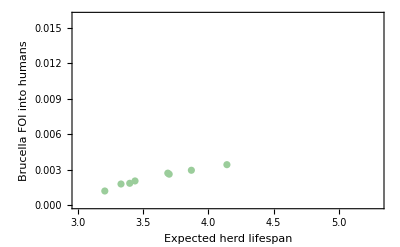

```mathematica
KajPlot=ListPlot[FitSpillModel[[1;;8,{3,4}]],PlotStyle->CMYKColor[0.243902,0.,0.243902,0.196078],PlotRange->{{3,5.3},{0,.016}},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Expected herd lifespan","Brucella FOI into humans"},BaseStyle->FontSize->14,ImageSize->400]
```

```mathematica
KajFit= Fit[FitSpillModel[[1;;8,{3,4}]], {1,x},x]
```

-0.00594929+0.00229675 x

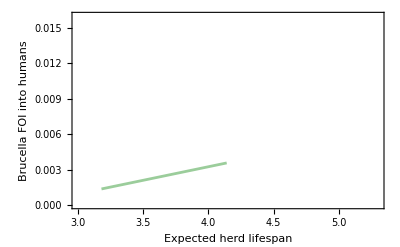

```mathematica
KajFitPlot=Plot[KajFit,{x,3.18,4.14},PlotStyle->CMYKColor[0.243902,0.,0.243902,0.196078],PlotRange->{{3,5.3},{0,.016}},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Expected herd lifespan","Brucella FOI into humans"},BaseStyle->FontSize->14,ImageSize->400]
```

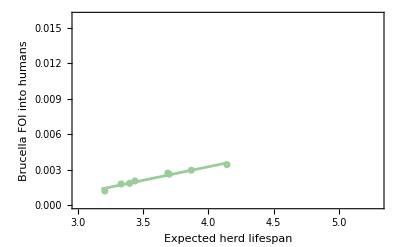

```mathematica
FullKajPlot=Show[{KajPlot,KajFitPlot},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Expected herd lifespan","Brucella FOI into humans"},BaseStyle->FontSize->14,ImageSize->400]
```

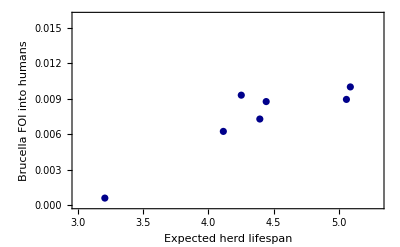

```mathematica
MarsPlot=ListPlot[FitSpillModel[[9;;15,{3,4}]],PlotStyle->CMYKColor[1.,1.,0.,0.454902],PlotRange->{{3.0,5.3},{0,.016}},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Expected herd lifespan","Brucella FOI into humans"},BaseStyle->FontSize->14,ImageSize->400]
```

```mathematica
MarsFit= Fit[FitSpillModel[[9;;15,{3,4}]], {1,x},x]
```

-0.0125264+0.00454217 x

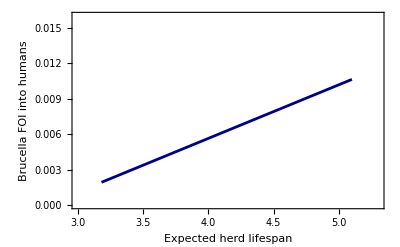

```mathematica
MarsFitPlot=Plot[MarsFit,{x,3.18,5.1},PlotStyle->CMYKColor[1.,1.,0.,0.454902],PlotRange->{{3,5.3},{0,.016}},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Expected herd lifespan","Brucella FOI into humans"},BaseStyle->FontSize->14,ImageSize->400]
```

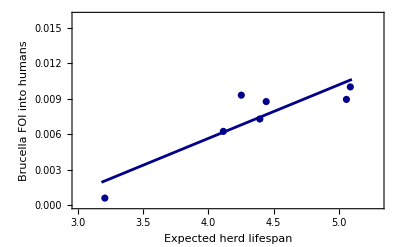

```mathematica
FullMarsPlot=Show[{MarsPlot,MarsFitPlot}]
```

```mathematica
MyLegend=LineLegend[{CMYKColor[0.14,0.92,1,0.34],CMYKColor[0.5,0.19,0.5,0.39]},{"Marsabit","Kajiado"}]
```

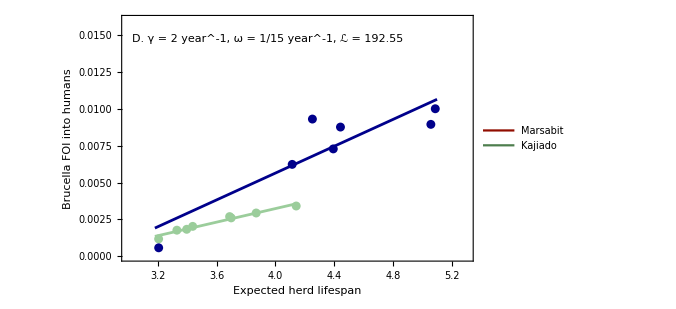

```mathematica
PlotMLDG2O15=Show[{FullKajPlot,FullMarsPlot},ImageSize->500,Epilog->{Inset[MyLegend,{5.1,0.03}],Inset["D. γ = 2 year^-1, ω = 1/15 year^-1, ℒ = 192.55",{3.95,0.0147}]}]
```

#### Next, simulate the scenario where acute infection lasts 2 years and antibodies last for 5 years

```mathematica
Module[{i,j},VillagePreds={{"County","Village","SPCamT","SPCowT","SPSheepT","SPGoatT","SPCamP","SPCowP","SPSheepP","SPGoatP","ELife","FOI","TrueFOI"}};For[j=2,j<=Length[ToSim],j++,Parms={Subscript[b, w]->ToSim[[j,3]],Subscript[b, x]->ToSim[[j,4]],Subscript[b, y]->ToSim[[j,5]],Subscript[b, z]->ToSim[[j,6]],Subscript[μ, w]->ToSim[[j,7]],Subscript[μ, x]->ToSim[[j,8]],Subscript[μ, y]->ToSim[[j,9]],Subscript[μ, z]->ToSim[[j,10]],β->MLDG2O5HAT[[6]],𝒜->MLDG2O5HAT[[5]],ρ->MLDG2O5HAT[[7]],γ->1/(2*365),ω->1/(5*365),kmars->1,kkaj->1};If[ToSim[[j,1]]=="Kajiado",ThisSol=NSolve[QSSEQKaj/.Parms,QSSEQVarKaj,PositiveReals,Method->"Monodromy"][[1]],ThisSol=NSolve[QSSEQMars/.Parms,QSSEQVarMars,PositiveReals,Method->"Monodromy"][[1]]];If[ToSim[[j,1]]=="Kajiado",VillagePreds=Append[VillagePreds,Join[{ToSim[[j,1]],ToSim[[j,2]],0,N[VD[[j,13]]/VD[[j,9]]],N[VD[[j,16]]/VD[[j,12]]],N[VD[[j,15]]/VD[[j,11]]]},SeroPrevIndiKaj/.ThisSol/.Parms,{N[Lifespans[[j-1]]]},{SpillForceTotalKaj/.ThisSol/.Parms},{VD[[j,31]]}]],VillagePreds=Append[VillagePreds,Join[{ToSim[[j,1]],ToSim[[j,2]],N[VD[[j,14]]/VD[[j,10]]],N[VD[[j,13]]/VD[[j,9]]],N[VD[[j,16]]/VD[[j,12]]],N[VD[[j,15]]/VD[[j,11]]]},SeroPrevIndiMars/.ThisSol/.Parms,{N[Lifespans[[j-1]]]},{SpillForceTotalMars/.ThisSol/.Parms},{VD[[j,31]]}]]]]]
```

```mathematica
MatrixForm[VillagePreds]
```

(County | Village | SPCamT | SPCowT | SPSheepT | SPGoatT | SPCamP | SPCowP | SPSheepP | SPGoatP | ELife | FOI | TrueFOI
Kajiado | Empukani | 0 | 0.0555556 | 0.01 | 0.0307692 | 0 | 0.0666761 | 0.0463385 | 0.0348614 | 3.43714 | 0.0886238 | 0.00226089
Kajiado | Endonyo | 0 | 0.0175439 | 0. | 0.0104167 | 0 | 0.0318721 | 0.02148 | 0.0159855 | 3.20545 | 0.0415164 | 0.00109665
Kajiado | Ilumbwa | 0 | 0. | 0. | 0.0126582 | 0 | 0.0882372 | 0.062532 | 0.0473809 | 3.69902 | 0.118824 | 0.00200433
Kajiado | Kikeleya | 0 | 0.117021 | 0. | 0.0210526 | 0 | 0.118546 | 0.086406 | 0.0661686 | 4.14163 | 0.162722 | 0.00322205
Kajiado | Kisrket | 0 | 0.0675676 | 0. | 0.00694444 | 0 | 0.0947573 | 0.0675554 | 0.0513011 | 3.68856 | 0.12812 | 0.00446998
Kajiado | Mailwa | 0 | 0.142857 | 0.012987 | 0.0253165 | 0 | 0.0524187 | 0.03597 | 0.0269384 | 3.32969 | 0.0690903 | 0.00146145
Kajiado | Olchurai | 0 | 0.0597015 | 0. | 0.028169 | 0 | 0.101916 | 0.0731408 | 0.0556803 | 3.86919 | 0.138418 | 0.00172166
Kajiado | Sere | 0 | 0.037037 | 0.0190476 | 0. | 0 | 0.0592467 | 0.0409027 | 0.0306987 | 3.39659 | 0.078403 | 0.00249274
Marsabit | Laisamis | 0.0422535 | 0.142857 | 0.0285714 | 0.104167 | 0.116936 | 0.103787 | 0.0746127 | 0.056838 | 5.05791 | 0.21834 | 0.0105524
Marsabit | Lontolio | 0.0982143 | 0.153846 | 0.0126582 | 0.104167 | 0.0993307 | 0.0844393 | 0.0596335 | 0.0451268 | 4.39394 | 0.179034 | 0.00576678
Marsabit | Nairibi | 0.0555556 | 0.0465116 | 0. | 0.0194175 | 0.00864818 | 0.0060387 | 0.00398033 | 0.00293984 | 3.20578 | 0.0134646 | 0.0065861
Marsabit | Ndikir | 0.0559006 | 0.0793651 | 0.0747664 | 0.10241 | 0.112915 | 0.0992185 | 0.0710275 | 0.0540208 | 4.44278 | 0.209086 | 0.00773889
Marsabit | Sakardala | 0.110448 | 0.164835 | 0.05 | 0.112426 | 0.127381 | 0.116092 | 0.0844226 | 0.0645925 | 5.08792 | 0.243213 | 0.0114247
Marsabit | Silapani | 0.0691489 | 0.0744681 | 0.0181818 | 0.0774194 | 0.0918249 | 0.0766789 | 0.0537725 | 0.0405866 | 4.11426 | 0.163166 | 0.0066115
Marsabit | Trigamo | 0.125945 | 0.116279 | 0.0505618 | 0.0960265 | 0.119754 | 0.107043 | 0.0771866 | 0.058866 | 4.25183 | 0.224929 | 0.00773983)

Check predicted vs true livestock seroprevalence:

```mathematica
Correlation[VillagePreds[[2;;All,{3,7}]]]
```

{{1.,0.871561},{0.871561,1.}}

```mathematica
Correlation[VillagePreds[[2;;All,{4,8}]]]
```

{{1.,0.471973},{0.471973,1.}}

```mathematica
Correlation[VillagePreds[[2;;All,{5,9}]]]
```

{{1.,0.412626},{0.412626,1.}}

```mathematica
Correlation[VillagePreds[[2;;All,{6,10}]]]
```

{{1.,0.497027},{0.497027,1.}}

Check the correlation between predicted and observed FOI

```mathematica
Correlation[VillagePreds[[2;;All,{12,13}]]]
```

{{1.,0.712935},{0.712935,1.}}

```mathematica
Correlation[VillagePreds[[2;;9,{12,13}]]]
```

{{1.,0.597598},{0.597598,1.}}

```mathematica
Correlation[VillagePreds[[10;;16,{12,13}]]]
```

{{1.,0.559141},{0.559141,1.}}

Estimate spillover coefficients by minimizing the summed square error between predicted and observed FOI:

```mathematica
SSE=Sum[(kkaj*VillagePreds[[i,12]]-VillagePreds[[i,13]])^2,{i,2,9}]+Sum[(kmars*VillagePreds[[i,12]]-VillagePreds[[i,13]])^2,{i,10,16}]
```

(-0.00109665+0.0415164 kkaj)^2+(-0.00146145+0.0690903 kkaj)^2+(-0.00249274+0.078403 kkaj)^2+(-0.00226089+0.0886238 kkaj)^2+(-0.00200433+0.118824 kkaj)^2+(-0.00446998+0.12812 kkaj)^2+(-0.00172166+0.138418 kkaj)^2+(-0.00322205+0.162722 kkaj)^2+(-0.0065861+0.0134646 kmars)^2+(-0.0066115+0.163166 kmars)^2+(-0.00576678+0.179034 kmars)^2+(-0.00773889+0.209086 kmars)^2+(-0.0105524+0.21834 kmars)^2+(-0.00773983+0.224929 kmars)^2+(-0.0114247+0.243213 kmars)^2

```mathematica
SpillCos=NMinimize[SSE,{kkaj,kmars}]
```

{0.0000521564,{kkaj→0.0218865,kmars→0.0409303}}

Generate quantitative predictions for FOI using the estimated values of the spillover coefficients:

```mathematica
FitSpillModel=Join[Table[{VillagePreds[[i,1]],VillagePreds[[i,2]],VillagePreds[[i,11]],kkaj*VillagePreds[[i,12]]},{i,2,9}],Table[{VillagePreds[[i,1]],VillagePreds[[i,2]],VillagePreds[[i,11]],kmars*VillagePreds[[i,12]]},{i,10,16}]]/.SpillCos[[2]];
```

```mathematica
MatrixForm[FitSpillModel]
```

(Kajiado | Empukani | 3.43714 | 0.00193966
Kajiado | Endonyo | 3.20545 | 0.000908649
Kajiado | Ilumbwa | 3.69902 | 0.00260064
Kajiado | Kikeleya | 4.14163 | 0.00356141
Kajiado | Kisrket | 3.68856 | 0.00280411
Kajiado | Mailwa | 3.32969 | 0.00151215
Kajiado | Olchurai | 3.86919 | 0.00302949
Kajiado | Sere | 3.39659 | 0.00171597
Marsabit | Laisamis | 5.05791 | 0.00893673
Marsabit | Lontolio | 4.39394 | 0.00732791
Marsabit | Nairibi | 3.20578 | 0.000551109
Marsabit | Ndikir | 4.44278 | 0.00855794
Marsabit | Sakardala | 5.08792 | 0.00995476
Marsabit | Silapani | 4.11426 | 0.00667844
Marsabit | Trigamo | 4.25183 | 0.0092064)

Plot predicted FOI as a function of expected livestock lifespan:

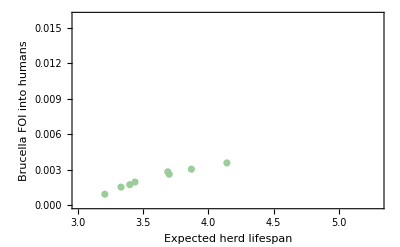

```mathematica
KajPlot=ListPlot[FitSpillModel[[1;;8,{3,4}]],PlotStyle->CMYKColor[0.243902,0.,0.243902,0.196078],PlotRange->{{3,5.3},{0,.016}},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Expected herd lifespan","Brucella FOI into humans"},BaseStyle->FontSize->14,ImageSize->400]
```

```mathematica
KajFit= Fit[FitSpillModel[[1;;8,{3,4}]], {1,x},x]
```

-0.00774678+0.00278255 x

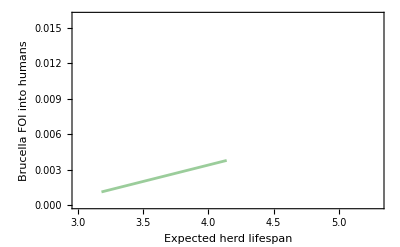

```mathematica
KajFitPlot=Plot[KajFit,{x,3.18,4.14},PlotStyle->CMYKColor[0.243902,0.,0.243902,0.196078],PlotRange->{{3,5.3},{0,.016}},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Expected herd lifespan","Brucella FOI into humans"},BaseStyle->FontSize->14,ImageSize->400]
```

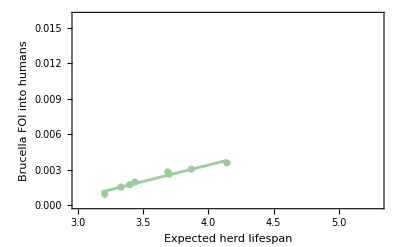

```mathematica
FullKajPlot=Show[{KajPlot,KajFitPlot},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Expected herd lifespan","Brucella FOI into humans"},BaseStyle->FontSize->14,ImageSize->400]
```

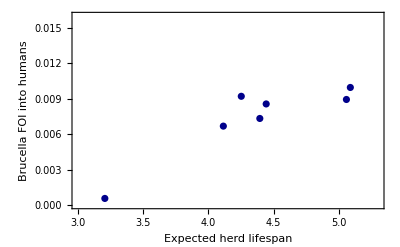

```mathematica
MarsPlot=ListPlot[FitSpillModel[[9;;15,{3,4}]],PlotStyle->CMYKColor[1.,1.,0.,0.454902],PlotRange->{{3.0,5.3},{0,.016}},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Expected herd lifespan","Brucella FOI into humans"},BaseStyle->FontSize->14,ImageSize->400]
```

```mathematica
MarsFit= Fit[FitSpillModel[[9;;15,{3,4}]], {1,x},x]
```

-0.0122982+0.00449365 x

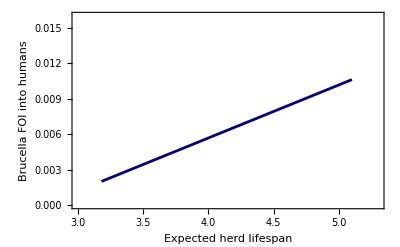

```mathematica
MarsFitPlot=Plot[MarsFit,{x,3.18,5.1},PlotStyle->CMYKColor[1.,1.,0.,0.454902],PlotRange->{{3,5.3},{0,.016}},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Expected herd lifespan","Brucella FOI into humans"},BaseStyle->FontSize->14,ImageSize->400]
```

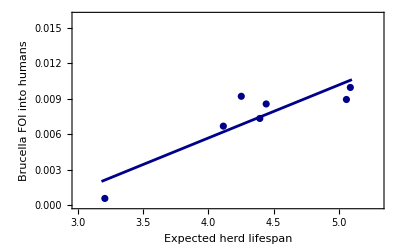

```mathematica
FullMarsPlot=Show[{MarsPlot,MarsFitPlot}]
```

```mathematica
MyLegend=LineLegend[{CMYKColor[0.14,0.92,1,0.34],CMYKColor[0.5,0.19,0.5,0.39]},{"Marsabit","Kajiado"}]
```

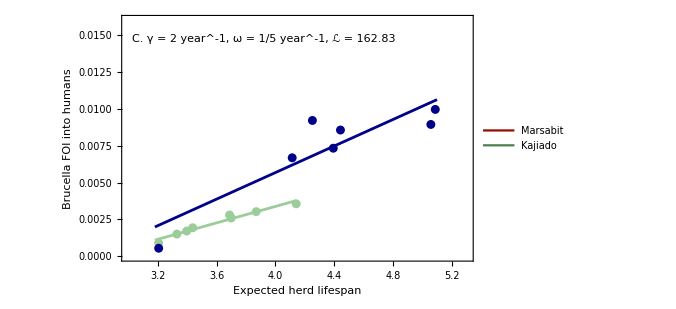

```mathematica
PlotMLDG2O5=Show[{FullKajPlot,FullMarsPlot},ImageSize->500,Epilog->{Inset[MyLegend,{5.1,0.03}],Inset["C. γ = 2 year^-1, ω = 1/5 year^-1, ℒ = 162.83",{3.92,0.0147}]}]
```

#### Then simulate for the scenario where acute infection lasts 0.5 years and antibodies 15 years

```mathematica
Module[{i,j},VillagePreds={{"County","Village","SPCamT","SPCowT","SPSheepT","SPGoatT","SPCamP","SPCowP","SPSheepP","SPGoatP","ELife","FOI","TrueFOI"}};For[j=2,j<=Length[ToSim],j++,Parms={Subscript[b, w]->ToSim[[j,3]],Subscript[b, x]->ToSim[[j,4]],Subscript[b, y]->ToSim[[j,5]],Subscript[b, z]->ToSim[[j,6]],Subscript[μ, w]->ToSim[[j,7]],Subscript[μ, x]->ToSim[[j,8]],Subscript[μ, y]->ToSim[[j,9]],Subscript[μ, z]->ToSim[[j,10]],β->MLDGHO15HAT[[6]],𝒜->MLDGHO15HAT[[5]],ρ->MLDGHO15HAT[[7]],γ->1/(0.5*365),ω->1/(15.0*365),kmars->1,kkaj->1};If[ToSim[[j,1]]=="Kajiado",ThisSol=NSolve[QSSEQKaj/.Parms,QSSEQVarKaj,PositiveReals,Method->"Monodromy"],ThisSol=NSolve[QSSEQMars/.Parms,QSSEQVarMars,PositiveReals,Method->"Monodromy"]];If[Length[ThisSol]>1,ThisSol=ThisSol[[2]],ThisSol=ThisSol[[1]]];If[ToSim[[j,1]]=="Kajiado",VillagePreds=Append[VillagePreds,Join[{ToSim[[j,1]],ToSim[[j,2]],0,N[VD[[j,13]]/VD[[j,9]]],N[VD[[j,16]]/VD[[j,12]]],N[VD[[j,15]]/VD[[j,11]]]},SeroPrevIndiKaj/.ThisSol/.Parms,{N[Lifespans[[j-1]]]},{SpillForceTotalKaj/.ThisSol/.Parms},{VD[[j,31]]}]],VillagePreds=Append[VillagePreds,Join[{ToSim[[j,1]],ToSim[[j,2]],N[VD[[j,14]]/VD[[j,10]]],N[VD[[j,13]]/VD[[j,9]]],N[VD[[j,16]]/VD[[j,12]]],N[VD[[j,15]]/VD[[j,11]]]},SeroPrevIndiMars/.ThisSol/.Parms,{N[Lifespans[[j-1]]]},{SpillForceTotalMars/.ThisSol/.Parms},{VD[[j,31]]}]]]]]
```

```mathematica
MatrixForm[VillagePreds]
```

(County | Village | SPCamT | SPCowT | SPSheepT | SPGoatT | SPCamP | SPCowP | SPSheepP | SPGoatP | ELife | FOI | TrueFOI
Kajiado | Empukani | 0 | 0.0555556 | 0.01 | 0.0307692 | 0 | 0.0550465 | 0.0332863 | 0.0237603 | 3.43714 | 0.0187566 | 0.00226089
Kajiado | Endonyo | 0 | 0.0175439 | 0. | 0.0104167 | 0 | 0.0258705 | 0.0153282 | 0.0108647 | 3.20545 | 0.00868542 | 0.00109665
Kajiado | Ilumbwa | 0 | 0. | 0. | 0.0126582 | 0 | 0.0628752 | 0.0382314 | 0.0273435 | 3.69902 | 0.0215114 | 0.00200433
Kajiado | Kikeleya | 0 | 0.117021 | 0. | 0.0210526 | 0 | 0.0804753 | 0.0495519 | 0.0355991 | 4.14163 | 0.0277895 | 0.00322205
Kajiado | Kisrket | 0 | 0.0675676 | 0. | 0.00694444 | 0 | 0.0815013 | 0.0502207 | 0.0360891 | 3.68856 | 0.0281592 | 0.00446998
Kajiado | Mailwa | 0 | 0.142857 | 0.012987 | 0.0253165 | 0 | 0.0374637 | 0.0223765 | 0.0159043 | 3.32969 | 0.0126511 | 0.00146145
Kajiado | Olchurai | 0 | 0.0597015 | 0. | 0.028169 | 0 | 0.0737389 | 0.0451854 | 0.0324059 | 3.86919 | 0.0253725 | 0.00172166
Kajiado | Sere | 0 | 0.037037 | 0.0190476 | 0. | 0 | 0.047712 | 0.0287027 | 0.0204515 | 3.39659 | 0.0161962 | 0.00249274
Marsabit | Laisamis | 0.0422535 | 0.142857 | 0.0285714 | 0.104167 | 0.115277 | 0.0744574 | 0.0456491 | 0.0327445 | 5.05791 | 0.036638 | 0.0105524
Marsabit | Lontolio | 0.0982143 | 0.153846 | 0.0126582 | 0.104167 | 0.104543 | 0.0664808 | 0.0405275 | 0.0290119 | 4.39394 | 0.0327714 | 0.00576678
Marsabit | Nairibi | 0.0555556 | 0.0465116 | 0. | 0.0194175 | 0.0188105 | 0.0106479 | 0.00624316 | 0.00440948 | 3.20578 | 0.00534427 | 0.0065861
Marsabit | Ndikir | 0.0559006 | 0.0793651 | 0.0747664 | 0.10241 | 0.133508 | 0.0885947 | 0.0548714 | 0.039504 | 4.44278 | 0.0434761 | 0.00773889
Marsabit | Sakardala | 0.110448 | 0.164835 | 0.05 | 0.112426 | 0.145106 | 0.097998 | 0.0611105 | 0.0441051 | 5.08792 | 0.0480181 | 0.0114247
Marsabit | Silapani | 0.0691489 | 0.0744681 | 0.0181818 | 0.0774194 | 0.118482 | 0.0768881 | 0.0472215 | 0.0338935 | 4.11426 | 0.0378149 | 0.0066115
Marsabit | Trigamo | 0.125945 | 0.116279 | 0.0505618 | 0.0960265 | 0.170835 | 0.120099 | 0.0761162 | 0.0552655 | 4.25183 | 0.0586924 | 0.00773983)

Check predicted vs true livestock seroprevalence:

```mathematica
Correlation[VillagePreds[[2;;All,{3,7}]]]
```

{{1.,0.90778},{0.90778,1.}}

```mathematica
Correlation[VillagePreds[[2;;All,{4,8}]]]
```

{{1.,0.450673},{0.450673,1.}}

```mathematica
Correlation[VillagePreds[[2;;All,{5,9}]]]
```

{{1.,0.605491},{0.605491,1.}}

```mathematica
Correlation[VillagePreds[[2;;All,{6,10}]]]
```

{{1.,0.618023},{0.618023,1.}}

Check the correlation between predicted and observed FOI

```mathematica
Correlation[VillagePreds[[2;;All,{12,13}]]]
```

{{1.,0.706739},{0.706739,1.}}

```mathematica
Correlation[VillagePreds[[2;;9,{12,13}]]]
```

{{1.,0.750508},{0.750508,1.}}

```mathematica
Correlation[VillagePreds[[10;;16,{12,13}]]]
```

{{1.,0.387779},{0.387779,1.}}

Estimate spillover coefficients by minimizing the summed square error between predicted and observed FOI

```mathematica
SSE=Sum[(kkaj*VillagePreds[[i,12]]-VillagePreds[[i,13]])^2,{i,2,9}]+Sum[(kmars*VillagePreds[[i,12]]-VillagePreds[[i,13]])^2,{i,10,16}]
```

(-0.00109665+0.00868542 kkaj)^2+(-0.00146145+0.0126511 kkaj)^2+(-0.00249274+0.0161962 kkaj)^2+(-0.00226089+0.0187566 kkaj)^2+(-0.00200433+0.0215114 kkaj)^2+(-0.00172166+0.0253725 kkaj)^2+(-0.00322205+0.0277895 kkaj)^2+(-0.00446998+0.0281592 kkaj)^2+(-0.0065861+0.00534427 kmars)^2+(-0.00576678+0.0327714 kmars)^2+(-0.0105524+0.036638 kmars)^2+(-0.0066115+0.0378149 kmars)^2+(-0.00773889+0.0434761 kmars)^2+(-0.0114247+0.0480181 kmars)^2+(-0.00773983+0.0586924 kmars)^2

```mathematica
SpillCos=NMinimize[SSE,{kkaj,kmars}]
```

{0.0000652324,{kkaj→0.117286,kmars→0.191058}}

Generate quantitative predictions for FOI using the estimated values of the spillover coefficients:

```mathematica
FitSpillModel=Join[Table[{VillagePreds[[i,1]],VillagePreds[[i,2]],VillagePreds[[i,11]],kkaj*VillagePreds[[i,12]]},{i,2,9}],Table[{VillagePreds[[i,1]],VillagePreds[[i,2]],VillagePreds[[i,11]],kmars*VillagePreds[[i,12]]},{i,10,16}]]/.SpillCos[[2]];
```

```mathematica
MatrixForm[%]
```

(Kajiado | Empukani | 3.43714 | 0.0021999
Kajiado | Endonyo | 3.20545 | 0.00101868
Kajiado | Ilumbwa | 3.69902 | 0.002523
Kajiado | Kikeleya | 4.14163 | 0.00325933
Kajiado | Kisrket | 3.68856 | 0.00330269
Kajiado | Mailwa | 3.32969 | 0.00148381
Kajiado | Olchurai | 3.86919 | 0.00297585
Kajiado | Sere | 3.39659 | 0.0018996
Marsabit | Laisamis | 5.05791 | 0.00699998
Marsabit | Lontolio | 4.39394 | 0.00626123
Marsabit | Nairibi | 3.20578 | 0.00102106
Marsabit | Ndikir | 4.44278 | 0.00830645
Marsabit | Sakardala | 5.08792 | 0.00917424
Marsabit | Silapani | 4.11426 | 0.00722484
Marsabit | Trigamo | 4.25183 | 0.0112136)

Plot predicted FOI as a function of expected livestock lifespan:

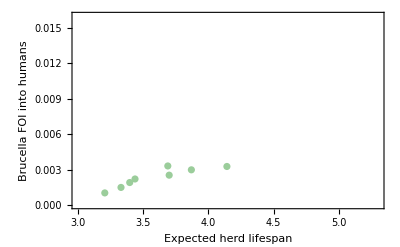

```mathematica
KajPlot=ListPlot[FitSpillModel[[1;;8,{3,4}]],PlotStyle->CMYKColor[0.243902,0.,0.243902,0.196078],PlotRange->{{3,5.3},{0,.016}},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Expected herd lifespan","Brucella FOI into humans"},BaseStyle->FontSize->14,ImageSize->400]
```

```mathematica
KajFit= Fit[FitSpillModel[[1;;8,{3,4}]], {1,x},x]
```

-0.00632621+0.00240803 x

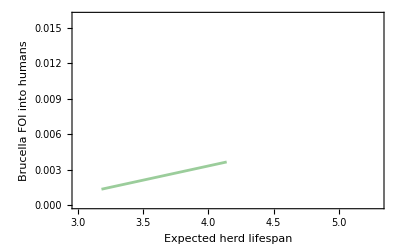

```mathematica
KajFitPlot=Plot[KajFit,{x,3.18,4.14},PlotStyle->CMYKColor[0.243902,0.,0.243902,0.196078],PlotRange->{{3,5.3},{0,.016}},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Expected herd lifespan","Brucella FOI into humans"},BaseStyle->FontSize->14,ImageSize->400]
```

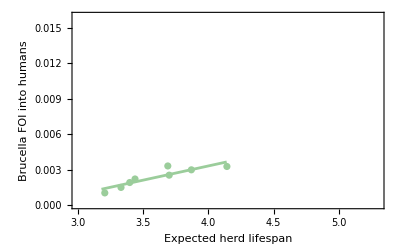

```mathematica
FullKajPlot=Show[{KajPlot,KajFitPlot},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Expected herd lifespan","Brucella FOI into humans"},BaseStyle->FontSize->14,ImageSize->400]
```

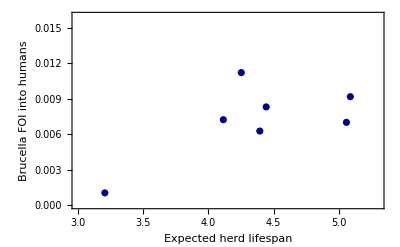

```mathematica
MarsPlot=ListPlot[FitSpillModel[[9;;15,{3,4}]],PlotStyle->CMYKColor[1.,1.,0.,0.454902],PlotRange->{{3.0,5.3},{0,.016}},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Expected herd lifespan","Brucella FOI into humans"},BaseStyle->FontSize->14,ImageSize->400]
```

```mathematica
MarsFit= Fit[FitSpillModel[[9;;15,{3,4}]], {1,x},x]
```

-0.0072933+0.00331391 x

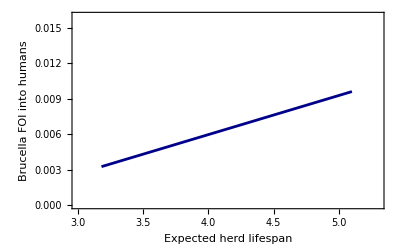

```mathematica
MarsFitPlot=Plot[MarsFit,{x,3.18,5.1},PlotStyle->CMYKColor[1.,1.,0.,0.454902],PlotRange->{{3,5.3},{0,.016}},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Expected herd lifespan","Brucella FOI into humans"},BaseStyle->FontSize->14,ImageSize->400]
```

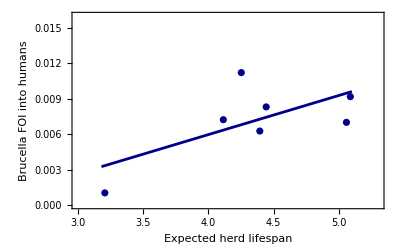

```mathematica
FullMarsPlot=Show[{MarsPlot,MarsFitPlot}]
```

```mathematica
MyLegend=LineLegend[{CMYKColor[0.14,0.92,1,0.34],CMYKColor[0.5,0.19,0.5,0.39]},{"Marsabit","Kajiado"}]
```

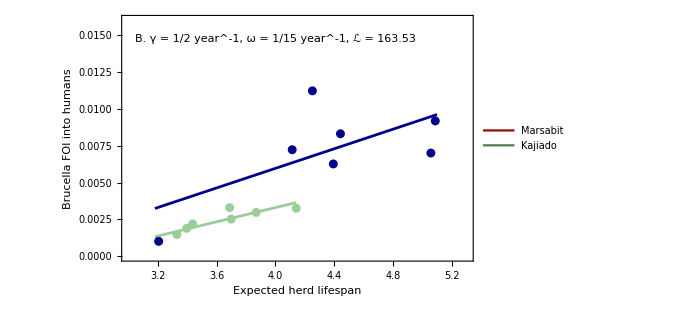

```mathematica
PlotMLDGHO15=Show[{FullKajPlot,FullMarsPlot},ImageSize->500,Epilog->{Inset[MyLegend,{5.1,0.03}],Inset["B. γ = 1/2 year^-1, ω = 1/15 year^-1, ℒ = 163.53",{4,0.0147}]}]
```

#### Then simulate for the scenario where acute infection lasts 0.5 years and antibodies 5 years

```mathematica
Module[{i,j},VillagePreds={{"County","Village","SPCamT","SPCowT","SPSheepT","SPGoatT","SPCamP","SPCowP","SPSheepP","SPGoatP","ELife","FOI","TrueFOI"}};For[j=2,j<=Length[ToSim],j++,Parms={Subscript[b, w]->ToSim[[j,3]],Subscript[b, x]->ToSim[[j,4]],Subscript[b, y]->ToSim[[j,5]],Subscript[b, z]->ToSim[[j,6]],Subscript[μ, w]->ToSim[[j,7]],Subscript[μ, x]->ToSim[[j,8]],Subscript[μ, y]->ToSim[[j,9]],Subscript[μ, z]->ToSim[[j,10]],β->MLDGHO5HAT[[6]],𝒜->MLDGHO5HAT[[5]],ρ->MLDGHO5HAT[[7]],γ->1/(0.5*365),ω->1/(5*365),kmars->1,kkaj->1};If[ToSim[[j,1]]=="Kajiado",ThisSol=NSolve[QSSEQKaj/.Parms,QSSEQVarKaj,PositiveReals,Method->"Monodromy"][[1]],ThisSol=NSolve[QSSEQMars/.Parms,QSSEQVarMars,PositiveReals,Method->"Monodromy"][[1]]];If[ToSim[[j,1]]=="Kajiado",VillagePreds=Append[VillagePreds,Join[{ToSim[[j,1]],ToSim[[j,2]],0,N[VD[[j,13]]/VD[[j,9]]],N[VD[[j,16]]/VD[[j,12]]],N[VD[[j,15]]/VD[[j,11]]]},SeroPrevIndiKaj/.ThisSol/.Parms,{N[Lifespans[[j-1]]]},{SpillForceTotalKaj/.ThisSol/.Parms},{VD[[j,31]]}]],VillagePreds=Append[VillagePreds,Join[{ToSim[[j,1]],ToSim[[j,2]],N[VD[[j,14]]/VD[[j,10]]],N[VD[[j,13]]/VD[[j,9]]],N[VD[[j,16]]/VD[[j,12]]],N[VD[[j,15]]/VD[[j,11]]]},SeroPrevIndiMars/.ThisSol/.Parms,{N[Lifespans[[j-1]]]},{SpillForceTotalMars/.ThisSol/.Parms},{VD[[j,31]]}]]]]]
```

```mathematica
MatrixForm[VillagePreds]
```

(County | Village | SPCamT | SPCowT | SPSheepT | SPGoatT | SPCamP | SPCowP | SPSheepP | SPGoatP | ELife | FOI | TrueFOI
Kajiado | Empukani | 0 | 0.0555556 | 0.01 | 0.0307692 | 0 | 0.0496747 | 0.0357327 | 0.0275655 | 3.43714 | 0.031908 | 0.00226089
Kajiado | Endonyo | 0 | 0.0175439 | 0. | 0.0104167 | 0 | 0.0198541 | 0.0138441 | 0.0105642 | 3.20545 | 0.0124847 | 0.00109665
Kajiado | Ilumbwa | 0 | 0. | 0. | 0.0126582 | 0 | 0.0609151 | 0.0443468 | 0.0343587 | 3.69902 | 0.0394549 | 0.00200433
Kajiado | Kikeleya | 0 | 0.117021 | 0. | 0.0210526 | 0 | 0.0817072 | 0.0608407 | 0.0475314 | 4.14163 | 0.0537669 | 0.00322205
Kajiado | Kisrket | 0 | 0.0675676 | 0. | 0.00694444 | 0 | 0.0765065 | 0.056645 | 0.0441597 | 3.68856 | 0.0501427 | 0.00446998
Kajiado | Mailwa | 0 | 0.142857 | 0.012987 | 0.0253165 | 0 | 0.0315236 | 0.0222479 | 0.0170479 | 3.32969 | 0.0199857 | 0.00146145
Kajiado | Olchurai | 0 | 0.0597015 | 0. | 0.028169 | 0 | 0.072755 | 0.0536478 | 0.0417599 | 3.86919 | 0.047547 | 0.00172166
Kajiado | Sere | 0 | 0.037037 | 0.0190476 | 0. | 0 | 0.0429256 | 0.0306585 | 0.0235912 | 3.39659 | 0.0274376 | 0.00249274
Marsabit | Laisamis | 0.0422535 | 0.142857 | 0.0285714 | 0.104167 | 0.0938452 | 0.0862732 | 0.0645642 | 0.0505356 | 5.05791 | 0.0878822 | 0.0105524
Marsabit | Lontolio | 0.0982143 | 0.153846 | 0.0126582 | 0.104167 | 0.0835678 | 0.0744635 | 0.0550097 | 0.0428495 | 4.39394 | 0.0762505 | 0.00576678
Marsabit | Nairibi | 0.0555556 | 0.0465116 | 0. | 0.0194175 | 0.0151169 | 0.0111808 | 0.00772739 | 0.00587886 | 3.20578 | 0.0119675 | 0.0065861
Marsabit | Ndikir | 0.0559006 | 0.0793651 | 0.0747664 | 0.10241 | 0.0987754 | 0.0922086 | 0.0694607 | 0.0545036 | 4.44278 | 0.0937111 | 0.00773889
Marsabit | Sakardala | 0.110448 | 0.164835 | 0.05 | 0.112426 | 0.108929 | 0.105029 | 0.0802603 | 0.0633256 | 5.08792 | 0.106281 | 0.0114247
Marsabit | Silapani | 0.0691489 | 0.0744681 | 0.0181818 | 0.0774194 | 0.0882636 | 0.0797681 | 0.0592707 | 0.0462681 | 4.11426 | 0.0814819 | 0.0066115
Marsabit | Trigamo | 0.125945 | 0.116279 | 0.0505618 | 0.0960265 | 0.115762 | 0.114141 | 0.0881284 | 0.0698144 | 4.25183 | 0.115213 | 0.00773983)

Check predicted vs true livestock seroprevalence:

```mathematica
Correlation[VillagePreds[[2;;All,{3,7}]]]
```

{{1.,0.89855},{0.89855,1.}}

```mathematica
Correlation[VillagePreds[[2;;All,{4,8}]]]
```

{{1.,0.526397},{0.526397,1.}}

```mathematica
Correlation[VillagePreds[[2;;All,{5,9}]]]
```

{{1.,0.633586},{0.633586,1.}}

```mathematica
Correlation[VillagePreds[[2;;All,{6,10}]]]
```

{{1.,0.720998},{0.720998,1.}}

Check the correlation between predicted and observed FOI

```mathematica
Correlation[VillagePreds[[2;;All,{12,13}]]]
```

{{1.,0.790399},{0.790399,1.}}

```mathematica
Correlation[VillagePreds[[2;;9,{12,13}]]]
```

{{1.,0.708318},{0.708318,1.}}

```mathematica
Correlation[VillagePreds[[10;;16,{12,13}]]]
```

{{1.,0.462346},{0.462346,1.}}

Estimate spillover coefficients by minimizing the summed square error between predicted and observed FOI

```mathematica
SSE=Sum[(kkaj*VillagePreds[[i,12]]-VillagePreds[[i,13]])^2,{i,2,9}]+Sum[(kmars*VillagePreds[[i,12]]-VillagePreds[[i,13]])^2,{i,10,16}]
```

(-0.00109665+0.0124847 kkaj)^2+(-0.00146145+0.0199857 kkaj)^2+(-0.00249274+0.0274376 kkaj)^2+(-0.00226089+0.031908 kkaj)^2+(-0.00200433+0.0394549 kkaj)^2+(-0.00172166+0.047547 kkaj)^2+(-0.00446998+0.0501427 kkaj)^2+(-0.00322205+0.0537669 kkaj)^2+(-0.0065861+0.0119675 kmars)^2+(-0.00576678+0.0762505 kmars)^2+(-0.0066115+0.0814819 kmars)^2+(-0.0105524+0.0878822 kmars)^2+(-0.00773889+0.0937111 kmars)^2+(-0.0114247+0.106281 kmars)^2+(-0.00773983+0.115213 kmars)^2

```mathematica
SpillCos=NMinimize[SSE,{kkaj,kmars}]
```

{0.0000542736,{kkaj→0.0642275,kmars→0.0897275}}

Generate quantitative predictions for FOI using the estimated values of the spillover coefficients:

```mathematica
FitSpillModel=Join[Table[{VillagePreds[[i,1]],VillagePreds[[i,2]],VillagePreds[[i,11]],kkaj*VillagePreds[[i,12]]},{i,2,9}],Table[{VillagePreds[[i,1]],VillagePreds[[i,2]],VillagePreds[[i,11]],kmars*VillagePreds[[i,12]]},{i,10,16}]]/.SpillCos[[2]];
```

```mathematica
MatrixForm[%]
```

(Kajiado | Empukani | 3.43714 | 0.00204937
Kajiado | Endonyo | 3.20545 | 0.000801858
Kajiado | Ilumbwa | 3.69902 | 0.00253409
Kajiado | Kikeleya | 4.14163 | 0.00345332
Kajiado | Kisrket | 3.68856 | 0.00322054
Kajiado | Mailwa | 3.32969 | 0.00128363
Kajiado | Olchurai | 3.86919 | 0.00305383
Kajiado | Sere | 3.39659 | 0.00176225
Marsabit | Laisamis | 5.05791 | 0.00788546
Marsabit | Lontolio | 4.39394 | 0.00684177
Marsabit | Nairibi | 3.20578 | 0.00107382
Marsabit | Ndikir | 4.44278 | 0.00840846
Marsabit | Sakardala | 5.08792 | 0.00953634
Marsabit | Silapani | 4.11426 | 0.00731117
Marsabit | Trigamo | 4.25183 | 0.0103378)

Plot predicted FOI as a function of expected livestock lifespan:

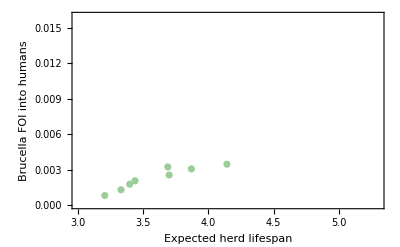

```mathematica
KajPlot=ListPlot[FitSpillModel[[1;;8,{3,4}]],PlotStyle->CMYKColor[0.243902,0.,0.243902,0.196078],PlotRange->{{3,5.3},{0,.016}},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Expected herd lifespan","Brucella FOI into humans"},BaseStyle->FontSize->14,ImageSize->400]
```

```mathematica
KajFit= Fit[FitSpillModel[[1;;8,{3,4}]], {1,x},x]
```

-0.00802821+0.00286383 x

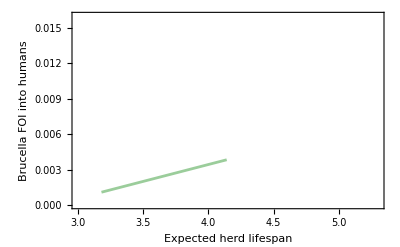

```mathematica
KajFitPlot=Plot[KajFit,{x,3.18,4.14},PlotStyle->CMYKColor[0.243902,0.,0.243902,0.196078],PlotRange->{{3,5.3},{0,.016}},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Expected herd lifespan","Brucella FOI into humans"},BaseStyle->FontSize->14,ImageSize->400]
```

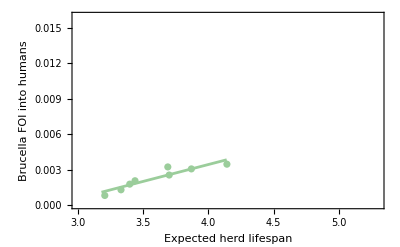

```mathematica
FullKajPlot=Show[{KajPlot,KajFitPlot},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Expected herd lifespan","Brucella FOI into humans"},BaseStyle->FontSize->14,ImageSize->400]
```

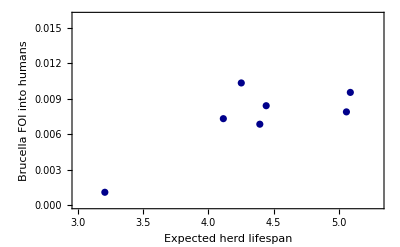

```mathematica
MarsPlot=ListPlot[FitSpillModel[[9;;15,{3,4}]],PlotStyle->CMYKColor[1.,1.,0.,0.454902],PlotRange->{{3.0,5.3},{0,.016}},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Expected herd lifespan","Brucella FOI into humans"},BaseStyle->FontSize->14,ImageSize->400]
```

```mathematica
MarsFit= Fit[FitSpillModel[[9;;15,{3,4}]], {1,x},x]
```

-0.00876966+0.0036912 x

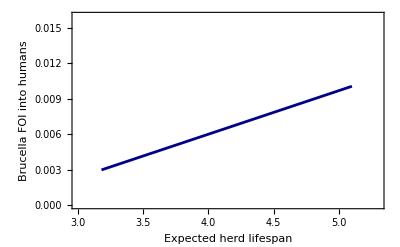

```mathematica
MarsFitPlot=Plot[MarsFit,{x,3.18,5.1},PlotStyle->CMYKColor[1.,1.,0.,0.454902],PlotRange->{{3,5.3},{0,.016}},Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},FrameLabel->{"Expected herd lifespan","Brucella FOI into humans"},BaseStyle->FontSize->14,ImageSize->400]
```

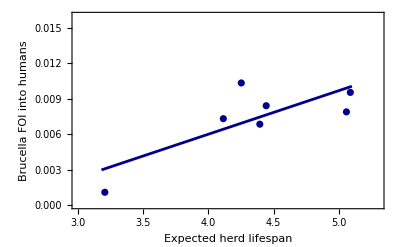

```mathematica
FullMarsPlot=Show[{MarsPlot,MarsFitPlot}]
```

```mathematica
MyLegend=LineLegend[{CMYKColor[1.,1.,0.,0.454902],CMYKColor[0.243902,0.,0.243902,0.196078]},{"Marsabit","Kajiado"}]
```

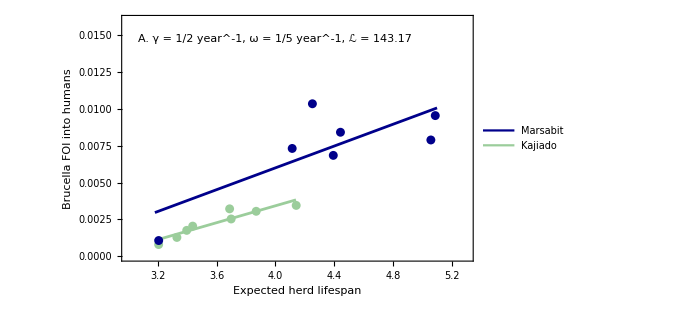

```mathematica
PlotMLDGHO5=Show[{FullKajPlot,FullMarsPlot},ImageSize->500,Epilog->{Inset[MyLegend,{4.85,0.003}],Inset["A. γ = 1/2 year^-1, ω = 1/5 year^-1, ℒ = 143.17",{4,0.0147}]}]
```

Generate a “clean” version of this figure with the best fit for the main text and export:

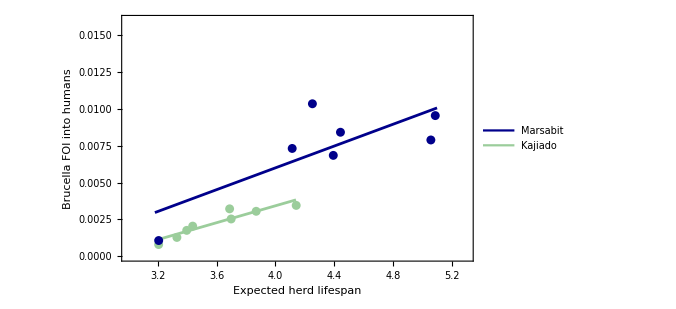

```mathematica
Figure5=Show[{FullKajPlot,FullMarsPlot},ImageSize->500,Epilog->{Inset[MyLegend,{4.85,0.003}]}]
```

```mathematica
Export[outpath<>"/Fig5.pdf",Figure5]
```

/home/nuismer/Work/Manuscripts/MTPOL/Figures/Fig5.pdf

#### Compare model fits across scenarios

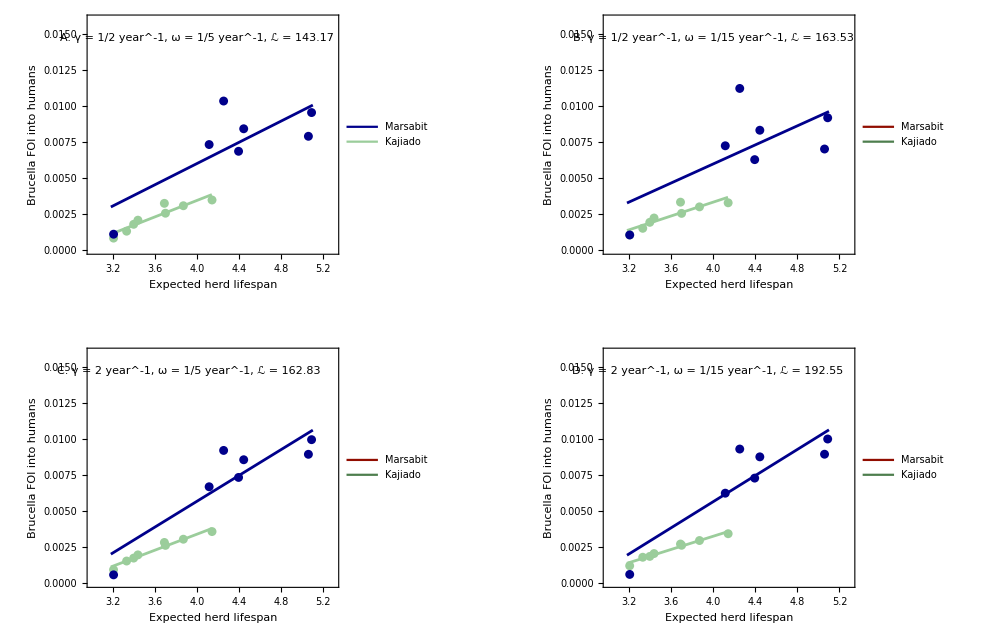

```mathematica
ModelCompare=GraphicsGrid[{{PlotMLDGHO5,PlotMLDGHO15},{PlotMLDG2O5,PlotMLDG2O15}},ImageSize->1000]
```

```mathematica
Export[outpath<>"/Model_Fit_Compare.pdf",ModelCompare]
```

/home/nuismer/Work/Manuscripts/MTPOL/Figures/Model_Fit_Compare.pdf